```mathematica
Conversion[(RightArrow | Rule | LongRightArrow)[A__,B__]] := Conversion/@{A,"->",B};
Conversion[(Equilibrium|ReverseEquilibrium|LeftRightArrow|LongLeftRightArrow| RightArrowLeftArrow| LeftArrowRightArrow)[A_,B__]] :=
Conversion/@{A,"⇌",Conversion[B]};
Conversion[(LeftArrow | LongLeftArrow)[A_,B_]] := Conversion/@{A,"<-",B};
Conversion[Sequence[A__]] := Riffle[List[A],"⇌"];

NotListQ[l_] := Head[l]=!=List;

SimplifyReactions[Reactions___] := 
Block[{$RecursionLimit = 10^3},
DeleteDuplicates[Flatten[
(Partition[#,3,2]&/@(Flatten[Conversion[#]]&/@{Reactions}))/.{{A_,"->",B_}->{{A,B}},{A_,"⇌",B_}-> {{A,B},{B,A}},{A_,"<-",B_}->{{B,A}}},2]]/.{A_?NotListQ, A_?NotListQ}->Sequence[]];

ReactionsData[Reactions___,ExternalSpecs_List:{}] := 
Module[{s=SimplifyReactions[Reactions],sp,ab,gamma,fhj,cpx,deficiency,var,kcoef,detmodel},
sp = Complement[Variables[(s/.r_*A_?StringQ ->A)//.(A_+B_)->{A,B}],Join[ExternalSpecs,{"0"}]];
Echo[sp];
{ab,fhj,cpx}= {Transpose/@ Transpose[Outer[Coefficient,s,sp]],s/.{A_?NotListQ,B_?NotListQ}->RightArrow[A,B],Union[Flatten[s]/.Thread[ExternalSpecs->0]]};
gamma=First[Differences[ab]];
{var,kcoef}={#[Symbol["t"]] &/@ (Subscript[Symbol["c"], #] & /@ sp),Array[Subscript[Symbol["k"], #]&, Length[ab[[1,1]]]]};
Echo[var];
Echo[# &/@ (Subscript[Symbol["c"], #] & /@ sp)];
Echo[#[0]==0 &/@ (Subscript[Symbol["c"], #] & /@ sp)];
Echo[kcoef];
detmodel=Thread[D[var,t] == gamma.(kcoef (Inner[Power,var,#,Times]&/@Transpose[First[ab]]))];
Echo[detmodel];
{fhj,Length[fhj],sp,Length[sp],ExternalSpecs,Length[ExternalSpecs],cpx,Length[cpx],Part[ab,1],Part[ab,2],gamma, Column[detmodel]}];

DescriptiveRK[l_List]:=
Module[{reac=ReactionsData@@l,h},
h=Part[reac,{4,2}];
Grid[MapThread[{#1,If[NumberQ[#2],#2,If[MatrixQ[#2],#2//MatrixForm,#2]]}&,{Data,reac}],Dividers->Center,FrameStyle->Directive[Brown],Spacings->{1,1.5},Alignment->{{Right,Left},Center},ItemStyle->{{Directive[Blue,13,Bold],Directive[Black,13,Bold]}},Background->{{Lighter[Yellow,.8],Lighter[Orange,.8]}}]];

Data={"complex chemical reaction","number of reaction steps","chemical species","number of chemical species","external species","number of external species","complexes","number of complexes",Column[{"matrix of reactant" ,"complex vectors (α)"},Right],Column[{"matrix of product","complex vectors (β)"},Right],"stoichiometric matrix (γ)",Column[{"induced mass action kinetic","differential equations","(CCD model)"},Right]};

Models = {"A + B → C","A + B ⇄ C","autocatalator","Belousov–Zhabotinsky",
"Brusselator","Eigen", "explodator","Feinberg–Horn I","Feinberg–Horn II","irreversible triangle reaction","reversible triangle reaction","Hudson–Rössler","Ivanova","Leonard–Reichl","Michaelis–Menten",
"Oregonator","Schlögl","Verhulst","Volterra–Lotka"};

BuiltInReactions =
Thread[Models->{
{A+B->C},{A+B⇄C},{A->X,X->Y,X+2Y->3Y,Y->P,{A,P}},
{X+Y+H->2W,Y+A+2H->X+W,2X->W,X+2A+2H->2X+2Z,2X+2Z->X,Z+O->Q,Z+W->Y,W->Y,{H,A,O,Q}},
{X←A,B+X->Y+D,Y+2X->3X,X->W,{A,B,D,W}},
{X->0,X->2X},{A+X->2X,X+Y-> Z,Z->2Y,Y->P,{A,P}},
{3X-> 2X+2Y-> 3Y-> 2X+Y-> 3X},{X⇌Y,X+Z-> T-> Y+ U->X+Z},
{C->A-> B->C},{A⇋B↔"C"⇄A},{P-> A,Q-> B,A+B->2B,B-> R,A↔C,{P,Q,R}},
{X+Y-> 2Y,Y+Z->2Z,X+Z->2Y},{2X⇆Y},
{"E"+S⇌C->"E"+P},{A+Y->X,X+Y->P,B+X->2X+Z,2X->Q,{A,P,B,Q}},{0⇌X,2X⇌3X},{X⇌2X},{X+A-> 2X,X+Y-> 2Y,B←Y,{A,B}}}];
```

```mathematica
(*cas13 pre-equilibration*)
```

```mathematica
(*rates of stuff*)
cas13Binding = 1;
cas13DissocGuide = 5;
cas13DissocSubs = 2000;
cas13DissocTarget = 1;
cas13Clevage = 200;
cas13Background = cas13Clevage/(5*10^8);
csm6ActivatorBinding = 1;
csm6ActivatorUnbinding = 63; (*Km from tina turn into kd at some point*)
csm6ActivatorCleavage = 0;
csm6Kcat = 0.4;
csm6SubstrateBinding = 1;
csm6SubstrateUnbinding = 5000;(*Kd? from tina turn maybe its a Km*)
csm6SubstrateUnbinding
```

5000

```mathematica
(*concentrations*)
reporterInitial = 200;
cas13Initial = 50;
guideInitial = 50;
rnpInitial = 0;
a4u6Initial = 2000;
csm6Initial = 100;
csm6Initial
```

100

```mathematica
rnpProduction = {{cas13 + guide ⇌ rnp, {cas13Binding, cas13DissocGuide}}};
Dimensions[rnpProduction]
eqs = rnpProduction[[All,1]]
DescriptiveRK[eqs]
rates = Flatten[rnpProduction[[All,2]]]
```

{1,2}

{cas13+guide⇌rnp}

{cas13,guide,rnp}

{c_cas13[t],c_guide[t],c_rnp[t]}

{c_cas13,c_guide,c_rnp}

{c_cas13[0]==0,c_guide[0]==0,c_rnp[0]==0}

{k_1,k_2}

{c_cas13'[t]==-k_1 c_cas13[t] c_guide[t]+k_2 c_rnp[t],c_guide'[t]==-k_1 c_cas13[t] c_guide[t]+k_2 c_rnp[t],c_rnp'[t]==k_1 c_cas13[t] c_guide[t]-k_2 c_rnp[t]}

complex chemical reaction | {cas13+guide→rnp,rnp→cas13+guide}
number of reaction steps | 2
chemical species | {cas13,guide,rnp}
number of chemical species | 3
external species | {}
number of external species | 0
complexes | {cas13+guide,rnp}
number of complexes | 2
matrix of reactant
complex vectors (α) | (1 | 0
1 | 0
0 | 1)
matrix of product
complex vectors (β) | (0 | 1
0 | 1
1 | 0)
stoichiometric matrix (γ) | (-1 | 1
-1 | 1
1 | -1)
induced mass action kinetic
differential equations
(CCD model) | c_cas13'[t]==-k_1 c_cas13[t] c_guide[t]+k_2 c_rnp[t]
c_guide'[t]==-k_1 c_cas13[t] c_guide[t]+k_2 c_rnp[t]
c_rnp'[t]==k_1 c_cas13[t] c_guide[t]-k_2 c_rnp[t]

{1,5}

```mathematica
diffEqs = {Subscript[c, cas13]'[t]==-Subscript[k, 1] Subscript[c, cas13][t] Subscript[c, guide][t]+Subscript[k, 2] Subscript[c, rnp][t],Subscript[c, guide]'[t]==-Subscript[k, 1] Subscript[c, cas13][t] Subscript[c, guide][t]+Subscript[k, 2] Subscript[c, rnp][t],Subscript[c, rnp]'[t]==Subscript[k, 1] Subscript[c, cas13][t] Subscript[c, guide][t]-Subscript[k, 2] Subscript[c, rnp][t]}/.Thread[{Subscript[k, 1],Subscript[k, 2]} -> rates]
```

{c_cas13'[t]==-c_cas13[t] c_guide[t]+5 c_rnp[t],c_guide'[t]==-c_cas13[t] c_guide[t]+5 c_rnp[t],c_rnp'[t]==c_cas13[t] c_guide[t]-5 c_rnp[t]}

```mathematica
initialConds = {Subscript[c, cas13][0]==cas13Initial,Subscript[c, guide][0]== guideInitial,Subscript[c, rnp][0]==0}
toSolve= Join[diffEqs,initialConds]
solved = NDSolve[toSolve, {Subscript[c, cas13],Subscript[c, guide],Subscript[c, rnp]},{t, 0, 2000},MaxStepSize -> 0.001]
```

{c_cas13[0]==50,c_guide[0]==50,c_rnp[0]==0}

{c_cas13'[t]==-c_cas13[t] c_guide[t]+5 c_rnp[t],c_guide'[t]==-c_cas13[t] c_guide[t]+5 c_rnp[t],c_rnp'[t]==c_cas13[t] c_guide[t]-5 c_rnp[t],c_cas13[0]==50,c_guide[0]==50,c_rnp[0]==0}

{{c_cas13→InterpolatingFunction[{{0., 2000.}}, <>],c_guide→InterpolatingFunction[{{0., 2000.}}, <>],c_rnp→InterpolatingFunction[{{0., 2000.}}, <>]}}

```mathematica
rnpf = Subscript[c, rnp]/.First@solved
cas13f = Subscript[c, cas13]/.First@solved
guidef = Subscript[c, guide]/.First@solved
```

InterpolatingFunction[{{0., 2000.}}, <>]

InterpolatingFunction[{{0., 2000.}}, <>]

InterpolatingFunction[{{0., 2000.}}, <>]

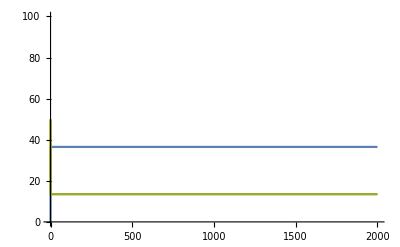

```mathematica
Plot[{rnpf[t],cas13f[t], guidef[t]},{t, 0, 2000},PlotRange->{0,100}]
```

```mathematica
rnpf[2000]
cas13f[2000]
guidef[2000]
```

36.4922

13.5078

13.5078

```mathematica
(*cas13 alone*)
```

```mathematica
(*concentrations*)
reporterInitial = 200;
cas13Initial = 13.507810593582104;
guideInitial = 13.507810593582104;
rnpInitial = 36.49218940641761;
a4u6Initial = 2000;
csm6Initial = 100;
csm6Initial
```

100

```mathematica
onTargetCas13 = {{cas13 + guide ⇌ rnp, {cas13Binding, cas13DissocGuide}},
{rnp + target ⇌ rnpActive, {cas13Binding, cas13DissocTarget}},
{rnpActive + reporter ⇌ rnpActivereporter, {cas13Binding, cas13DissocSubs}},
{rnpActivereporter -> rnpActive + product, {cas13Clevage}}
};
backgroundCas13 = {{rnp +reporter ⇌ rnpreporter, {cas13Binding, cas13DissocSubs}},
{rnpreporter -> rnp + product, {cas13Background}}
};

rxns = Join[onTargetCas13, backgroundCas13]
Dimensions[rxns]
eqs = rxns[[All,1]]
DescriptiveRK[eqs]
rates = Flatten[rxns[[All,2]]]
```

{{cas13+guide⇌rnp,{1,5}},{rnp+target⇌rnpActive,{1,1}},{reporter+rnpActive⇌rnpActivereporter,{1,2000}},{rnpActivereporter→product+rnpActive,{200}},{reporter+rnp⇌rnpreporter,{1,2000}},{rnpreporter→product+rnp,{1/2500000}}}

{6,2}

{cas13+guide⇌rnp,rnp+target⇌rnpActive,reporter+rnpActive⇌rnpActivereporter,rnpActivereporter→product+rnpActive,reporter+rnp⇌rnpreporter,rnpreporter→product+rnp}

{cas13,guide,product,reporter,rnp,rnpActive,rnpActivereporter,rnpreporter,target}

{c_cas13[t],c_guide[t],c_product[t],c_reporter[t],c_rnp[t],c_rnpActive[t],c_rnpActivereporter[t],c_rnpreporter[t],c_target[t]}

{c_cas13,c_guide,c_product,c_reporter,c_rnp,c_rnpActive,c_rnpActivereporter,c_rnpreporter,c_target}

{c_cas13[0]==0,c_guide[0]==0,c_product[0]==0,c_reporter[0]==0,c_rnp[0]==0,c_rnpActive[0]==0,c_rnpActivereporter[0]==0,c_rnpreporter[0]==0,c_target[0]==0}

{k_1,k_2,k_3,k_4,k_5,k_6,k_7,k_8,k_9,k_10}

{c_cas13'[t]==-k_1 c_cas13[t] c_guide[t]+k_2 c_rnp[t],c_guide'[t]==-k_1 c_cas13[t] c_guide[t]+k_2 c_rnp[t],c_product'[t]==k_7 c_rnpActivereporter[t]+k_10 c_rnpreporter[t],c_reporter'[t]==-k_8 c_reporter[t] c_rnp[t]-k_5 c_reporter[t] c_rnpActive[t]+k_6 c_rnpActivereporter[t]+k_9 c_rnpreporter[t],c_rnp'[t]==k_1 c_cas13[t] c_guide[t]-k_2 c_rnp[t]-k_8 c_reporter[t] c_rnp[t]+k_4 c_rnpActive[t]+k_9 c_rnpreporter[t]+k_10 c_rnpreporter[t]-k_3 c_rnp[t] c_target[t],c_rnpActive'[t]==-k_4 c_rnpActive[t]-k_5 c_reporter[t] c_rnpActive[t]+k_6 c_rnpActivereporter[t]+k_7 c_rnpActivereporter[t]+k_3 c_rnp[t] c_target[t],c_rnpActivereporter'[t]==k_5 c_reporter[t] c_rnpActive[t]-k_6 c_rnpActivereporter[t]-k_7 c_rnpActivereporter[t],c_rnpreporter'[t]==k_8 c_reporter[t] c_rnp[t]-k_9 c_rnpreporter[t]-k_10 c_rnpreporter[t],c_target'[t]==k_4 c_rnpActive[t]-k_3 c_rnp[t] c_target[t]}

complex chemical reaction | {cas13+guide→rnp,rnp→cas13+guide,rnp+target→rnpActive,rnpActive→rnp+target,reporter+rnpActive→rnpActivereporter,rnpActivereporter→reporter+rnpActive,rnpActivereporter→product+rnpActive,reporter+rnp→rnpreporter,rnpreporter→reporter+rnp,rnpreporter→product+rnp}
number of reaction steps | 10
chemical species | {cas13,guide,product,reporter,rnp,rnpActive,rnpActivereporter,rnpreporter,target}
number of chemical species | 9
external species | {}
number of external species | 0
complexes | {cas13+guide,rnp,product+rnp,reporter+rnp,rnpActive,product+rnpActive,reporter+rnpActive,rnpActivereporter,rnpreporter,rnp+target}
number of complexes | 10
matrix of reactant
complex vectors (α) | (1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
matrix of product
complex vectors (β) | (0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0)
stoichiometric matrix (γ) | (-1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | -1 | 1 | 0 | -1 | 1 | 0
1 | -1 | -1 | 1 | 0 | 0 | 0 | -1 | 1 | 1
0 | 0 | 1 | -1 | -1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | -1 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1
0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0)
induced mass action kinetic
differential equations
(CCD model) | c_cas13'[t]==-k_1 c_cas13[t] c_guide[t]+k_2 c_rnp[t]
c_guide'[t]==-k_1 c_cas13[t] c_guide[t]+k_2 c_rnp[t]
c_product'[t]==k_7 c_rnpActivereporter[t]+k_10 c_rnpreporter[t]
c_reporter'[t]==-k_8 c_reporter[t] c_rnp[t]-k_5 c_reporter[t] c_rnpActive[t]+k_6 c_rnpActivereporter[t]+k_9 c_rnpreporter[t]
c_rnp'[t]==k_1 c_cas13[t] c_guide[t]-k_2 c_rnp[t]-k_8 c_reporter[t] c_rnp[t]+k_4 c_rnpActive[t]+k_9 c_rnpreporter[t]+k_10 c_rnpreporter[t]-k_3 c_rnp[t] c_target[t]
c_rnpActive'[t]==-k_4 c_rnpActive[t]-k_5 c_reporter[t] c_rnpActive[t]+k_6 c_rnpActivereporter[t]+k_7 c_rnpActivereporter[t]+k_3 c_rnp[t] c_target[t]
c_rnpActivereporter'[t]==k_5 c_reporter[t] c_rnpActive[t]-k_6 c_rnpActivereporter[t]-k_7 c_rnpActivereporter[t]
c_rnpreporter'[t]==k_8 c_reporter[t] c_rnp[t]-k_9 c_rnpreporter[t]-k_10 c_rnpreporter[t]
c_target'[t]==k_4 c_rnpActive[t]-k_3 c_rnp[t] c_target[t]

{1,5,1,1,1,2000,200,1,2000,1/2500000}

```mathematica
diffEqs = {Subscript[c, cas13]'[t]==-Subscript[k, 1] Subscript[c, cas13][t] Subscript[c, guide][t]+Subscript[k, 2] Subscript[c, rnp][t],Subscript[c, guide]'[t]==-Subscript[k, 1] Subscript[c, cas13][t] Subscript[c, guide][t]+Subscript[k, 2] Subscript[c, rnp][t],Subscript[c, product]'[t]==Subscript[k, 7] Subscript[c, rnpActivereporter][t]+Subscript[k, 10] Subscript[c, rnpreporter][t],Subscript[c, reporter]'[t]==-Subscript[k, 8] Subscript[c, reporter][t] Subscript[c, rnp][t]-Subscript[k, 5] Subscript[c, reporter][t] Subscript[c, rnpActive][t]+Subscript[k, 6] Subscript[c, rnpActivereporter][t]+Subscript[k, 9] Subscript[c, rnpreporter][t],Subscript[c, rnp]'[t]==Subscript[k, 1] Subscript[c, cas13][t] Subscript[c, guide][t]-Subscript[k, 2] Subscript[c, rnp][t]-Subscript[k, 8] Subscript[c, reporter][t] Subscript[c, rnp][t]+Subscript[k, 4] Subscript[c, rnpActive][t]+Subscript[k, 9] Subscript[c, rnpreporter][t]+Subscript[k, 10] Subscript[c, rnpreporter][t]-Subscript[k, 3] Subscript[c, rnp][t] Subscript[c, target][t],Subscript[c, rnpActive]'[t]==-Subscript[k, 4] Subscript[c, rnpActive][t]-Subscript[k, 5] Subscript[c, reporter][t] Subscript[c, rnpActive][t]+Subscript[k, 6] Subscript[c, rnpActivereporter][t]+Subscript[k, 7] Subscript[c, rnpActivereporter][t]+Subscript[k, 3] Subscript[c, rnp][t] Subscript[c, target][t],Subscript[c, rnpActivereporter]'[t]==Subscript[k, 5] Subscript[c, reporter][t] Subscript[c, rnpActive][t]-Subscript[k, 6] Subscript[c, rnpActivereporter][t]-Subscript[k, 7] Subscript[c, rnpActivereporter][t],Subscript[c, rnpreporter]'[t]==Subscript[k, 8] Subscript[c, reporter][t] Subscript[c, rnp][t]-Subscript[k, 9] Subscript[c, rnpreporter][t]-Subscript[k, 10] Subscript[c, rnpreporter][t],Subscript[c, target]'[t]==Subscript[k, 4] Subscript[c, rnpActive][t]-Subscript[k, 3] Subscript[c, rnp][t] Subscript[c, target][t]}/.Thread[{Subscript[k, 1],Subscript[k, 2],Subscript[k, 3],Subscript[k, 4],Subscript[k, 5],Subscript[k, 6],Subscript[k, 7],Subscript[k, 8],Subscript[k, 9],Subscript[k, 10]} -> rates]
initialConds = {Subscript[c, cas13][0]==cas13Initial,Subscript[c, guide][0]==guideInitial,Subscript[c, product][0]==0,Subscript[c, reporter][0]==reporterInitial,Subscript[c, rnp][0]==rnpInitial,Subscript[c, rnpActive][0]==0,Subscript[c, rnpActivereporter][0]==0,Subscript[c, rnpreporter][0]==0,Subscript[c, target][0]==targetInitial}
toSolve= Join[diffEqs,initialConds]
getProduct[viralLoad_] :=  Subscript[c, product][t]/.NDSolve[toSolve/.Thread[{targetInitial} -> {viralLoad}], {Subscript[c, cas13],Subscript[c, guide],Subscript[c, product],Subscript[c, reporter],Subscript[c, rnp],Subscript[c, rnpActive],Subscript[c, rnpActivereporter],Subscript[c, rnpreporter],Subscript[c, target]},{t, 0, 2000},MaxStepSize -> 0.001]
```

{c_cas13'[t]==-c_cas13[t] c_guide[t]+5 c_rnp[t],c_guide'[t]==-c_cas13[t] c_guide[t]+5 c_rnp[t],c_product'[t]==200 c_rnpActivereporter[t]+c_rnpreporter[t]/2500000,c_reporter'[t]==-c_reporter[t] c_rnp[t]-c_reporter[t] c_rnpActive[t]+2000 c_rnpActivereporter[t]+2000 c_rnpreporter[t],c_rnp'[t]==c_cas13[t] c_guide[t]-5 c_rnp[t]-c_reporter[t] c_rnp[t]+c_rnpActive[t]+(5000000001 c_rnpreporter[t])/2500000-c_rnp[t] c_target[t],c_rnpActive'[t]==-c_rnpActive[t]-c_reporter[t] c_rnpActive[t]+2200 c_rnpActivereporter[t]+c_rnp[t] c_target[t],c_rnpActivereporter'[t]==c_reporter[t] c_rnpActive[t]-2200 c_rnpActivereporter[t],c_rnpreporter'[t]==c_reporter[t] c_rnp[t]-(5000000001 c_rnpreporter[t])/2500000,c_target'[t]==c_rnpActive[t]-c_rnp[t] c_target[t]}

{c_cas13[0]==13.5078,c_guide[0]==13.5078,c_product[0]==0,c_reporter[0]==200,c_rnp[0]==36.4922,c_rnpActive[0]==0,c_rnpActivereporter[0]==0,c_rnpreporter[0]==0,c_target[0]==targetInitial}

{c_cas13'[t]==-c_cas13[t] c_guide[t]+5 c_rnp[t],c_guide'[t]==-c_cas13[t] c_guide[t]+5 c_rnp[t],c_product'[t]==200 c_rnpActivereporter[t]+c_rnpreporter[t]/2500000,c_reporter'[t]==-c_reporter[t] c_rnp[t]-c_reporter[t] c_rnpActive[t]+2000 c_rnpActivereporter[t]+2000 c_rnpreporter[t],c_rnp'[t]==c_cas13[t] c_guide[t]-5 c_rnp[t]-c_reporter[t] c_rnp[t]+c_rnpActive[t]+(5000000001 c_rnpreporter[t])/2500000-c_rnp[t] c_target[t],c_rnpActive'[t]==-c_rnpActive[t]-c_reporter[t] c_rnpActive[t]+2200 c_rnpActivereporter[t]+c_rnp[t] c_target[t],c_rnpActivereporter'[t]==c_reporter[t] c_rnpActive[t]-2200 c_rnpActivereporter[t],c_rnpreporter'[t]==c_reporter[t] c_rnp[t]-(5000000001 c_rnpreporter[t])/2500000,c_target'[t]==c_rnpActive[t]-c_rnp[t] c_target[t],c_cas13[0]==13.5078,c_guide[0]==13.5078,c_product[0]==0,c_reporter[0]==200,c_rnp[0]==36.4922,c_rnpActive[0]==0,c_rnpActivereporter[0]==0,c_rnpreporter[0]==0,c_target[0]==targetInitial}

{b,{0,1/1000000000,1/100000000,1/10000000,1/1000000,1/100000,1/10000,1/1000,1/100,1/10,1}}

{{InterpolatingFunction[{{0., 2000.}}, <>][t]},{InterpolatingFunction[{{0., 2000.}}, <>][t]},{InterpolatingFunction[{{0., 2000.}}, <>][t]},{InterpolatingFunction[{{0., 2000.}}, <>][t]},{InterpolatingFunction[{{0., 2000.}}, <>][t]},{InterpolatingFunction[{{0., 2000.}}, <>][t]},{InterpolatingFunction[{{0., 2000.}}, <>][t]},{InterpolatingFunction[{{0., 2000.}}, <>][t]},{InterpolatingFunction[{{0., 2000.}}, <>][t]},{InterpolatingFunction[{{0., 2000.}}, <>][t]},{InterpolatingFunction[{{0., 2000.}}, <>][t]}}

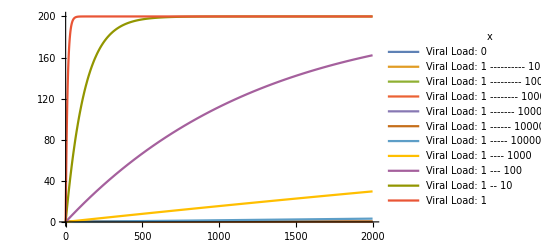

```mathematica
viralSweep = {b,{0,10^-9,10^-8, 10^-7, 10^-6, 10^-5, 10^-4 ,10^-3,10^-2,10^-1,10^0}}
resultTable=Evaluate@Table[getProduct[b],Evaluate@viralSweep]
Plot[Evaluate@resultTable,{t, 0, 2000},PlotLegends->LineLegend[Flatten[Table["Viral Load: "<>ToString[b],Evaluate@viralSweep], 1],LegendLabel->x], PlotRange->{0,200}]
```

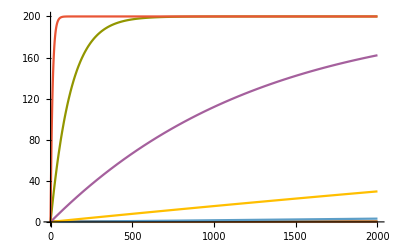

```mathematica
Plot[Evaluate@resultTable,{t, 0, 2000}, PlotRange->{0,200}]
```

```mathematica
getProduct[viralLoad_] :=  Subscript[c, product]/.NDSolve[toSolve/.Thread[{targetInitial} -> {viralLoad}], {Subscript[c, cas13],Subscript[c, guide],Subscript[c, product],Subscript[c, reporter],Subscript[c, rnp],Subscript[c, rnpActive],Subscript[c, rnpActivereporter],Subscript[c, rnpreporter],Subscript[c, target]},{t, 0, 2000},MaxStepSize -> 0.001]
viralSweep = {b,{0,10^-9,10^-8, 10^-7, 10^-6, 10^-5, 10^-4 ,10^-3,10^-2,10^-1,10^0}}
resultTable=Evaluate@Table[getProduct[b],Evaluate@viralSweep]
(*Plot[Evaluate@Map[#[t],resultTable],{t, 0, 2000}, PlotRange->{0,200}]
Plot[Evaluate@Map[#'[t],resultTable],{t, 0, 2000}, PlotRange->{0,200}]*)
```

{b,{0,1/1000000000,1/100000000,1/10000000,1/1000000,1/100000,1/10000,1/1000,1/100,1/10,1}}

{{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]}}

```mathematica
Map[Function[x,x[t]],resultTable, {2}]
```

{{InterpolatingFunction[{{0., 2000.}}, <>][t]},{InterpolatingFunction[{{0., 2000.}}, <>][t]},{InterpolatingFunction[{{0., 2000.}}, <>][t]},{InterpolatingFunction[{{0., 2000.}}, <>][t]},{InterpolatingFunction[{{0., 2000.}}, <>][t]},{InterpolatingFunction[{{0., 2000.}}, <>][t]},{InterpolatingFunction[{{0., 2000.}}, <>][t]},{InterpolatingFunction[{{0., 2000.}}, <>][t]},{InterpolatingFunction[{{0., 2000.}}, <>][t]},{InterpolatingFunction[{{0., 2000.}}, <>][t]},{InterpolatingFunction[{{0., 2000.}}, <>][t]}}

-Graphics-

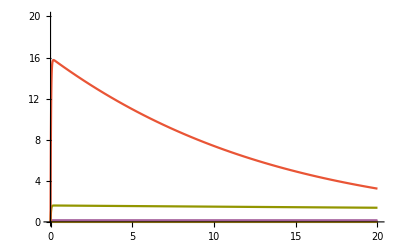

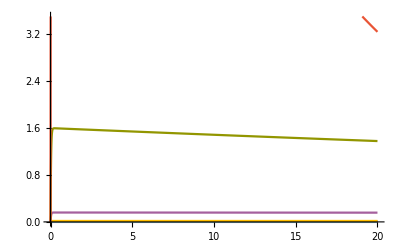

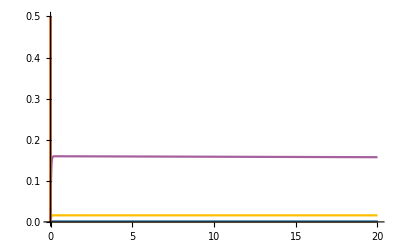

```mathematica
Plot[Evaluate@Map[Function[x,x[t]],resultTable, {2}],{t, 0, 2000}, PlotRange->{0,200}]
Plot[Evaluate@Map[Function[x,x'[t]],resultTable, {2}],{t, 0, 20}, PlotRange->{0,20}]
Plot[Evaluate@Map[Function[x,x'[t]],resultTable, {2}],{t, 0, 20}, PlotRange->{0,3.5}]
Plot[Evaluate@Map[Function[x,x'[t]],resultTable, {2}],{t, 0, 20}, PlotRange->{0,0.5}]
(*Plot[Evaluate@Map[Function[x,x''[t]],resultTable, {2}],{t, 0, 20}, PlotRange->{0,1}]*)
```

```mathematica
Map[Function[y, FindMaxValue[y,t]],Map[Function[x,x''[t]],resultTable, {2}]]
```

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaxValue::lstol will be suppressed during this calculation.

{-3.20682×10^-14,-3.21992×10^-14,-3.99566×10^-14,-1.57752×10^-13,-5.47109×10^-12,2.37826×10^-10,2.35011×10^-8,-1.1264×10^-6,-0.000117272,-0.0116637,-0.000285584}

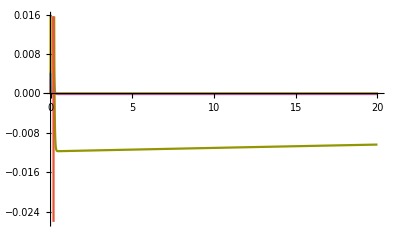

```mathematica
Plot[Evaluate@Map[Function[x,x''[t]],resultTable, {2}],{t, 0, 20}]
```

```mathematica
Map[Function[y, FindMaxValue[y,t]],Map[Function[x,x'[t]],resultTable, {2}]]
```

InterpolatingFunction::dmval: Input value {-19.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{1.32582×10^-6,1.34179×10^-6,1.48559×10^-6,2.92361×10^-6,0.0000173038,0.000161105,0.00159911,0.0159788,0.159743,1.59483,15.7572}

```mathematica
Map[Function[y, FindMaximum[y,{t,1}]],Map[Function[x,x'[t]],resultTable, {2}]]
```

InterpolatingFunction::dmval: Input value {-19.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{{1.32582×10^-6,{t→1.}},{1.34179×10^-6,{t→1.}},{1.48559×10^-6,{t→1.}},{2.92361×10^-6,{t→1.}},{0.0000173038,{t→1.}},{0.000161105,{t→1.}},{0.00159911,{t→0.999965}},{0.0159788,{t→0.378427}},{0.159743,{t→0.311887}},{1.59483,{t→0.245671}},{15.7572,{t→0.181473}}}

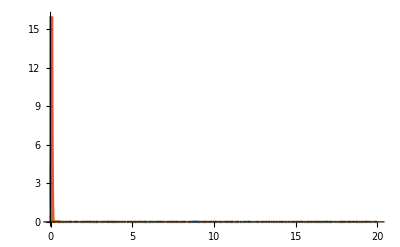

```mathematica
Plot[Evaluate@Map[Function[x,x''[t]],resultTable, {2}],{t, 0, 20}, PlotRange->{0,16}]
```

```mathematica
(*csm6 secondary*)
csm6ActivatorCleavage=0;
onTargetCas13 = {{cas13 + guide ⇌ rnp, {cas13Binding, cas13DissocTarget}},
{rnp + target ⇌ rnpActive, {cas13Binding, cas13DissocTarget}},
{rnpActive + a4u6 ⇌ rnpActivea4u6, {cas13Binding, cas13DissocSubs}},
{rnpActivea4u6 -> rnpActive + a4, {cas13Clevage}}
};
backgroundCas13 = {{rnp +a4u6 ⇌ rnpa4u6, {cas13Binding, cas13DissocSubs}},
{rnpa4u6 -> rnp + a4, {cas13Background}}
};
csm6Reactions = {{csm6 + a4 ⇌ csm6Active, {csm6ActivatorBinding, csm6ActivatorUnbinding-csm6ActivatorCleavage}},
{csm6Active -> csm6, {csm6ActivatorCleavage}},
{csm6Active + reporter ⇌ csm6ActiveReporter, {csm6SubstrateBinding, csm6SubstrateUnbinding}},
{csm6ActiveReporter -> csm6Active +product, {csm6Kcat}}
};

rxns = Join[onTargetCas13, backgroundCas13, csm6Reactions]
Dimensions[rxns]
eqs = rxns[[All,1]]
DescriptiveRK[eqs]
rates = Flatten[rxns[[All,2]]]
```

{{cas13+guide⇌rnp,{1,1}},{rnp+target⇌rnpActive,{1,1}},{a4u6+rnpActive⇌rnpActivea4u6,{1,2000}},{rnpActivea4u6→a4+rnpActive,{200}},{a4u6+rnp⇌rnpa4u6,{1,2000}},{rnpa4u6→a4+rnp,{1/2500000}},{a4+csm6⇌csm6Active,{1,63}},{csm6Active→csm6,{0}},{csm6Active+reporter⇌csm6ActiveReporter,{1,5000}},{csm6ActiveReporter→csm6Active+product,{0.4}}}

{10,2}

{cas13+guide⇌rnp,rnp+target⇌rnpActive,a4u6+rnpActive⇌rnpActivea4u6,rnpActivea4u6→a4+rnpActive,a4u6+rnp⇌rnpa4u6,rnpa4u6→a4+rnp,a4+csm6⇌csm6Active,csm6Active→csm6,csm6Active+reporter⇌csm6ActiveReporter,csm6ActiveReporter→csm6Active+product}

{a4,a4u6,cas13,csm6,csm6Active,csm6ActiveReporter,guide,product,reporter,rnp,rnpa4u6,rnpActive,rnpActivea4u6,target}

{c_a4[t],c_a4u6[t],c_cas13[t],c_csm6[t],c_csm6Active[t],c_csm6ActiveReporter[t],c_guide[t],c_product[t],c_reporter[t],c_rnp[t],c_rnpa4u6[t],c_rnpActive[t],c_rnpActivea4u6[t],c_target[t]}

{c_a4,c_a4u6,c_cas13,c_csm6,c_csm6Active,c_csm6ActiveReporter,c_guide,c_product,c_reporter,c_rnp,c_rnpa4u6,c_rnpActive,c_rnpActivea4u6,c_target}

{c_a4[0]==0,c_a4u6[0]==0,c_cas13[0]==0,c_csm6[0]==0,c_csm6Active[0]==0,c_csm6ActiveReporter[0]==0,c_guide[0]==0,c_product[0]==0,c_reporter[0]==0,c_rnp[0]==0,c_rnpa4u6[0]==0,c_rnpActive[0]==0,c_rnpActivea4u6[0]==0,c_target[0]==0}

{k_1,k_2,k_3,k_4,k_5,k_6,k_7,k_8,k_9,k_10,k_11,k_12,k_13,k_14,k_15,k_16}

{c_a4'[t]==-k_11 c_a4[t] c_csm6[t]+k_12 c_csm6Active[t]+k_10 c_rnpa4u6[t]+k_7 c_rnpActivea4u6[t],c_a4u6'[t]==-k_8 c_a4u6[t] c_rnp[t]+k_9 c_rnpa4u6[t]-k_5 c_a4u6[t] c_rnpActive[t]+k_6 c_rnpActivea4u6[t],c_cas13'[t]==-k_1 c_cas13[t] c_guide[t]+k_2 c_rnp[t],c_csm6'[t]==-k_11 c_a4[t] c_csm6[t]+k_12 c_csm6Active[t]+k_13 c_csm6Active[t],c_csm6Active'[t]==k_11 c_a4[t] c_csm6[t]-k_12 c_csm6Active[t]-k_13 c_csm6Active[t]+k_15 c_csm6ActiveReporter[t]+k_16 c_csm6ActiveReporter[t]-k_14 c_csm6Active[t] c_reporter[t],c_csm6ActiveReporter'[t]==-k_15 c_csm6ActiveReporter[t]-k_16 c_csm6ActiveReporter[t]+k_14 c_csm6Active[t] c_reporter[t],c_guide'[t]==-k_1 c_cas13[t] c_guide[t]+k_2 c_rnp[t],c_product'[t]==k_16 c_csm6ActiveReporter[t],c_reporter'[t]==k_15 c_csm6ActiveReporter[t]-k_14 c_csm6Active[t] c_reporter[t],c_rnp'[t]==k_1 c_cas13[t] c_guide[t]-k_2 c_rnp[t]-k_8 c_a4u6[t] c_rnp[t]+k_9 c_rnpa4u6[t]+k_10 c_rnpa4u6[t]+k_4 c_rnpActive[t]-k_3 c_rnp[t] c_target[t],c_rnpa4u6'[t]==k_8 c_a4u6[t] c_rnp[t]-k_9 c_rnpa4u6[t]-k_10 c_rnpa4u6[t],c_rnpActive'[t]==-k_4 c_rnpActive[t]-k_5 c_a4u6[t] c_rnpActive[t]+k_6 c_rnpActivea4u6[t]+k_7 c_rnpActivea4u6[t]+k_3 c_rnp[t] c_target[t],c_rnpActivea4u6'[t]==k_5 c_a4u6[t] c_rnpActive[t]-k_6 c_rnpActivea4u6[t]-k_7 c_rnpActivea4u6[t],c_target'[t]==k_4 c_rnpActive[t]-k_3 c_rnp[t] c_target[t]}

complex chemical reaction | {cas13+guide→rnp,rnp→cas13+guide,rnp+target→rnpActive,rnpActive→rnp+target,a4u6+rnpActive→rnpActivea4u6,rnpActivea4u6→a4u6+rnpActive,rnpActivea4u6→a4+rnpActive,a4u6+rnp→rnpa4u6,rnpa4u6→a4u6+rnp,rnpa4u6→a4+rnp,a4+csm6→csm6Active,csm6Active→a4+csm6,csm6Active→csm6,csm6Active+reporter→csm6ActiveReporter,csm6ActiveReporter→csm6Active+reporter,csm6ActiveReporter→csm6Active+product}
number of reaction steps | 16
chemical species | {a4,a4u6,cas13,csm6,csm6Active,csm6ActiveReporter,guide,product,reporter,rnp,rnpa4u6,rnpActive,rnpActivea4u6,target}
number of chemical species | 14
external species | {}
number of external species | 0
complexes | {csm6,a4+csm6,csm6Active,csm6ActiveReporter,cas13+guide,csm6Active+product,csm6Active+reporter,rnp,a4+rnp,a4u6+rnp,rnpa4u6,rnpActive,a4+rnpActive,a4u6+rnpActive,rnpActivea4u6,rnp+target}
number of complexes | 16
matrix of reactant
complex vectors (α) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
matrix of product
complex vectors (β) | (0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
stoichiometric matrix (γ) | (0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | -1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 1 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | -1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1
-1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0
1 | -1 | -1 | 1 | 0 | 0 | 0 | -1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | -1 | -1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
induced mass action kinetic
differential equations
(CCD model) | c_a4'[t]==-k_11 c_a4[t] c_csm6[t]+k_12 c_csm6Active[t]+k_10 c_rnpa4u6[t]+k_7 c_rnpActivea4u6[t]
c_a4u6'[t]==-k_8 c_a4u6[t] c_rnp[t]+k_9 c_rnpa4u6[t]-k_5 c_a4u6[t] c_rnpActive[t]+k_6 c_rnpActivea4u6[t]
c_cas13'[t]==-k_1 c_cas13[t] c_guide[t]+k_2 c_rnp[t]
c_csm6'[t]==-k_11 c_a4[t] c_csm6[t]+k_12 c_csm6Active[t]+k_13 c_csm6Active[t]
c_csm6Active'[t]==k_11 c_a4[t] c_csm6[t]-k_12 c_csm6Active[t]-k_13 c_csm6Active[t]+k_15 c_csm6ActiveReporter[t]+k_16 c_csm6ActiveReporter[t]-k_14 c_csm6Active[t] c_reporter[t]
c_csm6ActiveReporter'[t]==-k_15 c_csm6ActiveReporter[t]-k_16 c_csm6ActiveReporter[t]+k_14 c_csm6Active[t] c_reporter[t]
c_guide'[t]==-k_1 c_cas13[t] c_guide[t]+k_2 c_rnp[t]
c_product'[t]==k_16 c_csm6ActiveReporter[t]
c_reporter'[t]==k_15 c_csm6ActiveReporter[t]-k_14 c_csm6Active[t] c_reporter[t]
c_rnp'[t]==k_1 c_cas13[t] c_guide[t]-k_2 c_rnp[t]-k_8 c_a4u6[t] c_rnp[t]+k_9 c_rnpa4u6[t]+k_10 c_rnpa4u6[t]+k_4 c_rnpActive[t]-k_3 c_rnp[t] c_target[t]
c_rnpa4u6'[t]==k_8 c_a4u6[t] c_rnp[t]-k_9 c_rnpa4u6[t]-k_10 c_rnpa4u6[t]
c_rnpActive'[t]==-k_4 c_rnpActive[t]-k_5 c_a4u6[t] c_rnpActive[t]+k_6 c_rnpActivea4u6[t]+k_7 c_rnpActivea4u6[t]+k_3 c_rnp[t] c_target[t]
c_rnpActivea4u6'[t]==k_5 c_a4u6[t] c_rnpActive[t]-k_6 c_rnpActivea4u6[t]-k_7 c_rnpActivea4u6[t]
c_target'[t]==k_4 c_rnpActive[t]-k_3 c_rnp[t] c_target[t]

{1,1,1,1,1,2000,200,1,2000,1/2500000,1,63,0,1,5000,0.4}

```mathematica
diffEqs = {Subscript[c, a4]'[t]==-Subscript[k, 11] Subscript[c, a4][t] Subscript[c, csm6][t]+Subscript[k, 12] Subscript[c, csm6Active][t]+Subscript[k, 10] Subscript[c, rnpa4u6][t]+Subscript[k, 7] Subscript[c, rnpActivea4u6][t],Subscript[c, a4u6]'[t]==-Subscript[k, 8] Subscript[c, a4u6][t] Subscript[c, rnp][t]+Subscript[k, 9] Subscript[c, rnpa4u6][t]-Subscript[k, 5] Subscript[c, a4u6][t] Subscript[c, rnpActive][t]+Subscript[k, 6] Subscript[c, rnpActivea4u6][t],Subscript[c, cas13]'[t]==-Subscript[k, 1] Subscript[c, cas13][t] Subscript[c, guide][t]+Subscript[k, 2] Subscript[c, rnp][t],Subscript[c, csm6]'[t]==-Subscript[k, 11] Subscript[c, a4][t] Subscript[c, csm6][t]+Subscript[k, 12] Subscript[c, csm6Active][t]+Subscript[k, 13] Subscript[c, csm6Active][t],Subscript[c, csm6Active]'[t]==Subscript[k, 11] Subscript[c, a4][t] Subscript[c, csm6][t]-Subscript[k, 12] Subscript[c, csm6Active][t]-Subscript[k, 13] Subscript[c, csm6Active][t]+Subscript[k, 15] Subscript[c, csm6ActiveReporter][t]+Subscript[k, 16] Subscript[c, csm6ActiveReporter][t]-Subscript[k, 14] Subscript[c, csm6Active][t] Subscript[c, reporter][t],Subscript[c, csm6ActiveReporter]'[t]==-Subscript[k, 15] Subscript[c, csm6ActiveReporter][t]-Subscript[k, 16] Subscript[c, csm6ActiveReporter][t]+Subscript[k, 14] Subscript[c, csm6Active][t] Subscript[c, reporter][t],Subscript[c, guide]'[t]==-Subscript[k, 1] Subscript[c, cas13][t] Subscript[c, guide][t]+Subscript[k, 2] Subscript[c, rnp][t],Subscript[c, product]'[t]==Subscript[k, 16] Subscript[c, csm6ActiveReporter][t],Subscript[c, reporter]'[t]==Subscript[k, 15] Subscript[c, csm6ActiveReporter][t]-Subscript[k, 14] Subscript[c, csm6Active][t] Subscript[c, reporter][t],Subscript[c, rnp]'[t]==Subscript[k, 1] Subscript[c, cas13][t] Subscript[c, guide][t]-Subscript[k, 2] Subscript[c, rnp][t]-Subscript[k, 8] Subscript[c, a4u6][t] Subscript[c, rnp][t]+Subscript[k, 9] Subscript[c, rnpa4u6][t]+Subscript[k, 10] Subscript[c, rnpa4u6][t]+Subscript[k, 4] Subscript[c, rnpActive][t]-Subscript[k, 3] Subscript[c, rnp][t] Subscript[c, target][t],Subscript[c, rnpa4u6]'[t]==Subscript[k, 8] Subscript[c, a4u6][t] Subscript[c, rnp][t]-Subscript[k, 9] Subscript[c, rnpa4u6][t]-Subscript[k, 10] Subscript[c, rnpa4u6][t],Subscript[c, rnpActive]'[t]==-Subscript[k, 4] Subscript[c, rnpActive][t]-Subscript[k, 5] Subscript[c, a4u6][t] Subscript[c, rnpActive][t]+Subscript[k, 6] Subscript[c, rnpActivea4u6][t]+Subscript[k, 7] Subscript[c, rnpActivea4u6][t]+Subscript[k, 3] Subscript[c, rnp][t] Subscript[c, target][t],Subscript[c, rnpActivea4u6]'[t]==Subscript[k, 5] Subscript[c, a4u6][t] Subscript[c, rnpActive][t]-Subscript[k, 6] Subscript[c, rnpActivea4u6][t]-Subscript[k, 7] Subscript[c, rnpActivea4u6][t],Subscript[c, target]'[t]==Subscript[k, 4] Subscript[c, rnpActive][t]-Subscript[k, 3] Subscript[c, rnp][t] Subscript[c, target][t]}/.Thread[{Subscript[k, 1],Subscript[k, 2],Subscript[k, 3],Subscript[k, 4],Subscript[k, 5],Subscript[k, 6],Subscript[k, 7],Subscript[k, 8],Subscript[k, 9],Subscript[k, 10],Subscript[k, 11],Subscript[k, 12],Subscript[k, 13],Subscript[k, 14],Subscript[k, 15],Subscript[k, 16]} -> rates]
initialConds = {Subscript[c, a4][0]==0,Subscript[c, a4u6][0]==a4u6Initial,Subscript[c, cas13][0]==cas13Initial,Subscript[c, csm6][0]==csm6Initial,Subscript[c, csm6Active][0]==0,Subscript[c, csm6ActiveReporter][0]==0,Subscript[c, guide][0]==guideInitial,Subscript[c, product][0]==0,Subscript[c, reporter][0]==reporterInitial,Subscript[c, rnp][0]==rnpInitial,Subscript[c, rnpa4u6][0]==0,Subscript[c, rnpActive][0]==0,Subscript[c, rnpActivea4u6][0]==0,Subscript[c, target][0]==targetInitial}
toSolve= Join[diffEqs,initialConds]
```

{c_a4'[t]==-c_a4[t] c_csm6[t]+63 c_csm6Active[t]+c_rnpa4u6[t]/2500000+200 c_rnpActivea4u6[t],c_a4u6'[t]==-c_a4u6[t] c_rnp[t]+2000 c_rnpa4u6[t]-c_a4u6[t] c_rnpActive[t]+2000 c_rnpActivea4u6[t],c_cas13'[t]==-c_cas13[t] c_guide[t]+c_rnp[t],c_csm6'[t]==-c_a4[t] c_csm6[t]+63 c_csm6Active[t],c_csm6Active'[t]==c_a4[t] c_csm6[t]-63 c_csm6Active[t]+5000.4 c_csm6ActiveReporter[t]-c_csm6Active[t] c_reporter[t],c_csm6ActiveReporter'[t]==-5000.4 c_csm6ActiveReporter[t]+c_csm6Active[t] c_reporter[t],c_guide'[t]==-c_cas13[t] c_guide[t]+c_rnp[t],c_product'[t]==0.4 c_csm6ActiveReporter[t],c_reporter'[t]==5000 c_csm6ActiveReporter[t]-c_csm6Active[t] c_reporter[t],c_rnp'[t]==c_cas13[t] c_guide[t]-c_rnp[t]-c_a4u6[t] c_rnp[t]+(5000000001 c_rnpa4u6[t])/2500000+c_rnpActive[t]-c_rnp[t] c_target[t],c_rnpa4u6'[t]==c_a4u6[t] c_rnp[t]-(5000000001 c_rnpa4u6[t])/2500000,c_rnpActive'[t]==-c_rnpActive[t]-c_a4u6[t] c_rnpActive[t]+2200 c_rnpActivea4u6[t]+c_rnp[t] c_target[t],c_rnpActivea4u6'[t]==c_a4u6[t] c_rnpActive[t]-2200 c_rnpActivea4u6[t],c_target'[t]==c_rnpActive[t]-c_rnp[t] c_target[t]}

{c_a4[0]==0,c_a4u6[0]==2000,c_cas13[0]==13.5078,c_csm6[0]==100,c_csm6Active[0]==0,c_csm6ActiveReporter[0]==0,c_guide[0]==13.5078,c_product[0]==0,c_reporter[0]==200,c_rnp[0]==36.4922,c_rnpa4u6[0]==0,c_rnpActive[0]==0,c_rnpActivea4u6[0]==0,c_target[0]==targetInitial}

{c_a4'[t]==-c_a4[t] c_csm6[t]+63 c_csm6Active[t]+c_rnpa4u6[t]/2500000+200 c_rnpActivea4u6[t],c_a4u6'[t]==-c_a4u6[t] c_rnp[t]+2000 c_rnpa4u6[t]-c_a4u6[t] c_rnpActive[t]+2000 c_rnpActivea4u6[t],c_cas13'[t]==-c_cas13[t] c_guide[t]+c_rnp[t],c_csm6'[t]==-c_a4[t] c_csm6[t]+63 c_csm6Active[t],c_csm6Active'[t]==c_a4[t] c_csm6[t]-63 c_csm6Active[t]+5000.4 c_csm6ActiveReporter[t]-c_csm6Active[t] c_reporter[t],c_csm6ActiveReporter'[t]==-5000.4 c_csm6ActiveReporter[t]+c_csm6Active[t] c_reporter[t],c_guide'[t]==-c_cas13[t] c_guide[t]+c_rnp[t],c_product'[t]==0.4 c_csm6ActiveReporter[t],c_reporter'[t]==5000 c_csm6ActiveReporter[t]-c_csm6Active[t] c_reporter[t],c_rnp'[t]==c_cas13[t] c_guide[t]-c_rnp[t]-c_a4u6[t] c_rnp[t]+(5000000001 c_rnpa4u6[t])/2500000+c_rnpActive[t]-c_rnp[t] c_target[t],c_rnpa4u6'[t]==c_a4u6[t] c_rnp[t]-(5000000001 c_rnpa4u6[t])/2500000,c_rnpActive'[t]==-c_rnpActive[t]-c_a4u6[t] c_rnpActive[t]+2200 c_rnpActivea4u6[t]+c_rnp[t] c_target[t],c_rnpActivea4u6'[t]==c_a4u6[t] c_rnpActive[t]-2200 c_rnpActivea4u6[t],c_target'[t]==c_rnpActive[t]-c_rnp[t] c_target[t],c_a4[0]==0,c_a4u6[0]==2000,c_cas13[0]==13.5078,c_csm6[0]==100,c_csm6Active[0]==0,c_csm6ActiveReporter[0]==0,c_guide[0]==13.5078,c_product[0]==0,c_reporter[0]==200,c_rnp[0]==36.4922,c_rnpa4u6[0]==0,c_rnpActive[0]==0,c_rnpActivea4u6[0]==0,c_target[0]==targetInitial}

{b,{0,1/1000000000,1/100000000,1/10000000,1/1000000,1/100000,1/10000,1/1000,1/100,1/10,1}}

{{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]}}

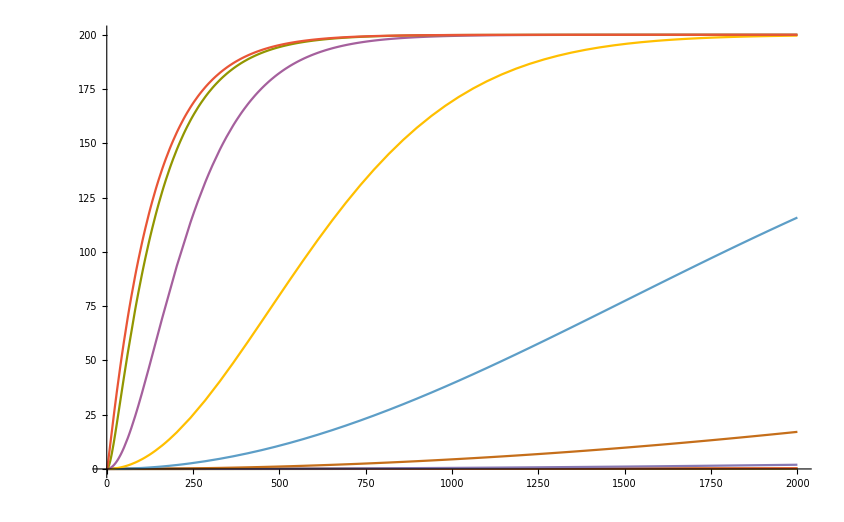

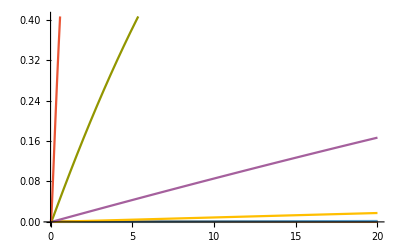

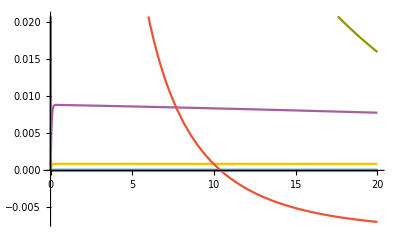

```mathematica
getProduct[viralLoad_] :=  Subscript[c, product]/.NDSolve[toSolve/.Thread[{targetInitial} -> {viralLoad}], {Subscript[c, a4],Subscript[c, a4u6],Subscript[c, cas13],Subscript[c, csm6],Subscript[c, csm6Active],Subscript[c, csm6ActiveReporter],Subscript[c, guide],Subscript[c, product],Subscript[c, reporter],Subscript[c, rnp],Subscript[c, rnpa4u6],Subscript[c, rnpActive],Subscript[c, rnpActivea4u6],Subscript[c, target]},{t, 0, 2000},MaxStepSize -> 0.001]
viralSweep = {b,{0,10^-9,10^-8, 10^-7, 10^-6, 10^-5, 10^-4 ,10^-3,10^-2,10^-1,10^0}}
resultTable=Evaluate@Table[getProduct[b],Evaluate@viralSweep]
Plot[Evaluate@Map[Function[x,x[t]],resultTable, {2}],{t, 0, 2000}, PlotRange->{0,200}]
Plot[Evaluate@Map[Function[x,x'[t]],resultTable, {2}],{t, 0, 20}]
Plot[Evaluate@Map[Function[x,x''[t]],resultTable, {2}],{t, 0, 20}]
```

```mathematica
Map[Function[y, FindMaxValue[y,t]],Map[Function[x,x'[t]],resultTable, {2}]]
Map[Function[y, FindMaxValue[y,t]],Map[Function[x,x''[t]],resultTable, {2}]]
```

InterpolatingFunction::dmval: Input value {2661.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaxValue::lstol will be suppressed during this calculation.

FindMaxValue::sdprec: Line search unable to find a sufficient increase in the function value with MachinePrecision digit precision.

{0.000172129,0.000173927,0.000176187,1767.16,0.00193082,6.83698×10^6,2.16863×10^24,0.235968,0.597133,1.04425,1.31853}

InterpolatingFunction::dmval: Input value {-19.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaxValue::lstol will be suppressed during this calculation.

{8.6173×10^-8,8.70595×10^-8,9.50376×10^-8,1.74819×10^-7,9.72633×10^-7,8.95074×10^-6,0.0000887281,0.00088632,0.00884791,0.0874421,0.810054}

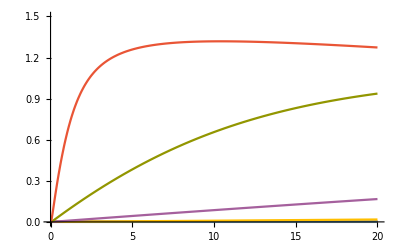

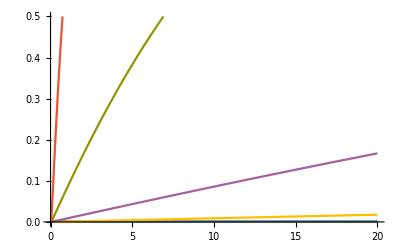

```mathematica
Plot[Evaluate@Map[Function[x,x'[t]],resultTable, {2}],{t, 0, 20}, PlotRange->{0,1.5}]
Plot[Evaluate@Map[Function[x,x'[t]],resultTable, {2}],{t, 0, 20}, PlotRange->{0,0.5}]
```

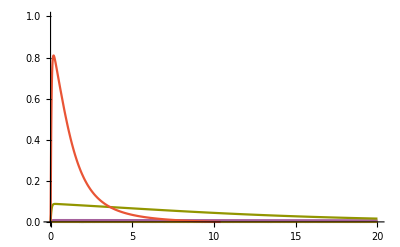

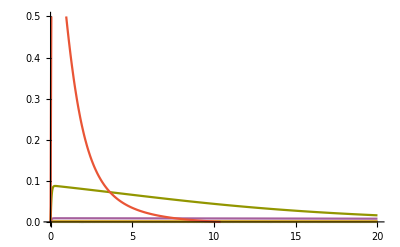

```mathematica
Plot[Evaluate@Map[Function[x,x''[t]],resultTable, {2}],{t, 0, 20}, PlotRange->{0,1}]
Plot[Evaluate@Map[Function[x,x''[t]],resultTable, {2}],{t, 0, 20}, PlotRange->{0,0.5}]
```

```mathematica
(*csm6 secondary activator cleavage*)
csm6ActivatorCleavage= cleavageRate;
onTargetCas13 = {{cas13 + guide ⇌ rnp, {cas13Binding, cas13DissocTarget}},
{rnp + target ⇌ rnpActive, {cas13Binding, cas13DissocTarget}},
{rnpActive + a4u6 ⇌ rnpActivea4u6, {cas13Binding, cas13DissocSubs}},
{rnpActivea4u6 -> rnpActive + a4, {cas13Clevage}}
};
backgroundCas13 = {{rnp +a4u6 ⇌ rnpa4u6, {cas13Binding, cas13DissocSubs}},
{rnpa4u6 -> rnp + a4, {cas13Background}}
};
csm6Reactions = {{csm6 + a4 ⇌ csm6Active, {csm6ActivatorBinding, csm6ActivatorUnbinding-csm6ActivatorCleavage}},
{csm6Active -> csm6, {csm6ActivatorCleavage}},
{csm6Active + reporter ⇌ csm6ActiveReporter, {csm6SubstrateBinding, csm6SubstrateUnbinding}},
{csm6ActiveReporter -> csm6Active +product, {csm6Kcat}}
};

rxns = Join[onTargetCas13, backgroundCas13, csm6Reactions]
Dimensions[rxns]
eqs = rxns[[All,1]]
DescriptiveRK[eqs]
rates = Flatten[rxns[[All,2]]]
```

{{cas13+guide⇌rnp,{1,1}},{rnp+target⇌rnpActive,{1,1}},{a4u6+rnpActive⇌rnpActivea4u6,{1,2000}},{rnpActivea4u6→a4+rnpActive,{200}},{a4u6+rnp⇌rnpa4u6,{1,2000}},{rnpa4u6→a4+rnp,{1/2500000}},{a4+csm6⇌csm6Active,{1,63-cleavageRate}},{csm6Active→csm6,{cleavageRate}},{csm6Active+reporter⇌csm6ActiveReporter,{1,5000}},{csm6ActiveReporter→csm6Active+product,{0.4}}}

{10,2}

{cas13+guide⇌rnp,rnp+target⇌rnpActive,a4u6+rnpActive⇌rnpActivea4u6,rnpActivea4u6→a4+rnpActive,a4u6+rnp⇌rnpa4u6,rnpa4u6→a4+rnp,a4+csm6⇌csm6Active,csm6Active→csm6,csm6Active+reporter⇌csm6ActiveReporter,csm6ActiveReporter→csm6Active+product}

{a4,a4u6,cas13,csm6,csm6Active,csm6ActiveReporter,guide,product,reporter,rnp,rnpa4u6,rnpActive,rnpActivea4u6,target}

{c_a4[t],c_a4u6[t],c_cas13[t],c_csm6[t],c_csm6Active[t],c_csm6ActiveReporter[t],c_guide[t],c_product[t],c_reporter[t],c_rnp[t],c_rnpa4u6[t],c_rnpActive[t],c_rnpActivea4u6[t],c_target[t]}

{c_a4,c_a4u6,c_cas13,c_csm6,c_csm6Active,c_csm6ActiveReporter,c_guide,c_product,c_reporter,c_rnp,c_rnpa4u6,c_rnpActive,c_rnpActivea4u6,c_target}

{c_a4[0]==0,c_a4u6[0]==0,c_cas13[0]==0,c_csm6[0]==0,c_csm6Active[0]==0,c_csm6ActiveReporter[0]==0,c_guide[0]==0,c_product[0]==0,c_reporter[0]==0,c_rnp[0]==0,c_rnpa4u6[0]==0,c_rnpActive[0]==0,c_rnpActivea4u6[0]==0,c_target[0]==0}

{k_1,k_2,k_3,k_4,k_5,k_6,k_7,k_8,k_9,k_10,k_11,k_12,k_13,k_14,k_15,k_16}

{c_a4'[t]==-k_11 c_a4[t] c_csm6[t]+k_12 c_csm6Active[t]+k_10 c_rnpa4u6[t]+k_7 c_rnpActivea4u6[t],c_a4u6'[t]==-k_8 c_a4u6[t] c_rnp[t]+k_9 c_rnpa4u6[t]-k_5 c_a4u6[t] c_rnpActive[t]+k_6 c_rnpActivea4u6[t],c_cas13'[t]==-k_1 c_cas13[t] c_guide[t]+k_2 c_rnp[t],c_csm6'[t]==-k_11 c_a4[t] c_csm6[t]+k_12 c_csm6Active[t]+k_13 c_csm6Active[t],c_csm6Active'[t]==k_11 c_a4[t] c_csm6[t]-k_12 c_csm6Active[t]-k_13 c_csm6Active[t]+k_15 c_csm6ActiveReporter[t]+k_16 c_csm6ActiveReporter[t]-k_14 c_csm6Active[t] c_reporter[t],c_csm6ActiveReporter'[t]==-k_15 c_csm6ActiveReporter[t]-k_16 c_csm6ActiveReporter[t]+k_14 c_csm6Active[t] c_reporter[t],c_guide'[t]==-k_1 c_cas13[t] c_guide[t]+k_2 c_rnp[t],c_product'[t]==k_16 c_csm6ActiveReporter[t],c_reporter'[t]==k_15 c_csm6ActiveReporter[t]-k_14 c_csm6Active[t] c_reporter[t],c_rnp'[t]==k_1 c_cas13[t] c_guide[t]-k_2 c_rnp[t]-k_8 c_a4u6[t] c_rnp[t]+k_9 c_rnpa4u6[t]+k_10 c_rnpa4u6[t]+k_4 c_rnpActive[t]-k_3 c_rnp[t] c_target[t],c_rnpa4u6'[t]==k_8 c_a4u6[t] c_rnp[t]-k_9 c_rnpa4u6[t]-k_10 c_rnpa4u6[t],c_rnpActive'[t]==-k_4 c_rnpActive[t]-k_5 c_a4u6[t] c_rnpActive[t]+k_6 c_rnpActivea4u6[t]+k_7 c_rnpActivea4u6[t]+k_3 c_rnp[t] c_target[t],c_rnpActivea4u6'[t]==k_5 c_a4u6[t] c_rnpActive[t]-k_6 c_rnpActivea4u6[t]-k_7 c_rnpActivea4u6[t],c_target'[t]==k_4 c_rnpActive[t]-k_3 c_rnp[t] c_target[t]}

complex chemical reaction | {cas13+guide→rnp,rnp→cas13+guide,rnp+target→rnpActive,rnpActive→rnp+target,a4u6+rnpActive→rnpActivea4u6,rnpActivea4u6→a4u6+rnpActive,rnpActivea4u6→a4+rnpActive,a4u6+rnp→rnpa4u6,rnpa4u6→a4u6+rnp,rnpa4u6→a4+rnp,a4+csm6→csm6Active,csm6Active→a4+csm6,csm6Active→csm6,csm6Active+reporter→csm6ActiveReporter,csm6ActiveReporter→csm6Active+reporter,csm6ActiveReporter→csm6Active+product}
number of reaction steps | 16
chemical species | {a4,a4u6,cas13,csm6,csm6Active,csm6ActiveReporter,guide,product,reporter,rnp,rnpa4u6,rnpActive,rnpActivea4u6,target}
number of chemical species | 14
external species | {}
number of external species | 0
complexes | {csm6,a4+csm6,csm6Active,csm6ActiveReporter,cas13+guide,csm6Active+product,csm6Active+reporter,rnp,a4+rnp,a4u6+rnp,rnpa4u6,rnpActive,a4+rnpActive,a4u6+rnpActive,rnpActivea4u6,rnp+target}
number of complexes | 16
matrix of reactant
complex vectors (α) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
matrix of product
complex vectors (β) | (0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
stoichiometric matrix (γ) | (0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | -1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 1 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | -1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1
-1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0
1 | -1 | -1 | 1 | 0 | 0 | 0 | -1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | -1 | -1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
induced mass action kinetic
differential equations
(CCD model) | c_a4'[t]==-k_11 c_a4[t] c_csm6[t]+k_12 c_csm6Active[t]+k_10 c_rnpa4u6[t]+k_7 c_rnpActivea4u6[t]
c_a4u6'[t]==-k_8 c_a4u6[t] c_rnp[t]+k_9 c_rnpa4u6[t]-k_5 c_a4u6[t] c_rnpActive[t]+k_6 c_rnpActivea4u6[t]
c_cas13'[t]==-k_1 c_cas13[t] c_guide[t]+k_2 c_rnp[t]
c_csm6'[t]==-k_11 c_a4[t] c_csm6[t]+k_12 c_csm6Active[t]+k_13 c_csm6Active[t]
c_csm6Active'[t]==k_11 c_a4[t] c_csm6[t]-k_12 c_csm6Active[t]-k_13 c_csm6Active[t]+k_15 c_csm6ActiveReporter[t]+k_16 c_csm6ActiveReporter[t]-k_14 c_csm6Active[t] c_reporter[t]
c_csm6ActiveReporter'[t]==-k_15 c_csm6ActiveReporter[t]-k_16 c_csm6ActiveReporter[t]+k_14 c_csm6Active[t] c_reporter[t]
c_guide'[t]==-k_1 c_cas13[t] c_guide[t]+k_2 c_rnp[t]
c_product'[t]==k_16 c_csm6ActiveReporter[t]
c_reporter'[t]==k_15 c_csm6ActiveReporter[t]-k_14 c_csm6Active[t] c_reporter[t]
c_rnp'[t]==k_1 c_cas13[t] c_guide[t]-k_2 c_rnp[t]-k_8 c_a4u6[t] c_rnp[t]+k_9 c_rnpa4u6[t]+k_10 c_rnpa4u6[t]+k_4 c_rnpActive[t]-k_3 c_rnp[t] c_target[t]
c_rnpa4u6'[t]==k_8 c_a4u6[t] c_rnp[t]-k_9 c_rnpa4u6[t]-k_10 c_rnpa4u6[t]
c_rnpActive'[t]==-k_4 c_rnpActive[t]-k_5 c_a4u6[t] c_rnpActive[t]+k_6 c_rnpActivea4u6[t]+k_7 c_rnpActivea4u6[t]+k_3 c_rnp[t] c_target[t]
c_rnpActivea4u6'[t]==k_5 c_a4u6[t] c_rnpActive[t]-k_6 c_rnpActivea4u6[t]-k_7 c_rnpActivea4u6[t]
c_target'[t]==k_4 c_rnpActive[t]-k_3 c_rnp[t] c_target[t]

{1,1,1,1,1,2000,200,1,2000,1/2500000,1,63-cleavageRate,cleavageRate,1,5000,0.4}

```mathematica
diffEqs = {Subscript[c, a4]'[t]==-Subscript[k, 11] Subscript[c, a4][t] Subscript[c, csm6][t]+Subscript[k, 12] Subscript[c, csm6Active][t]+Subscript[k, 10] Subscript[c, rnpa4u6][t]+Subscript[k, 7] Subscript[c, rnpActivea4u6][t],Subscript[c, a4u6]'[t]==-Subscript[k, 8] Subscript[c, a4u6][t] Subscript[c, rnp][t]+Subscript[k, 9] Subscript[c, rnpa4u6][t]-Subscript[k, 5] Subscript[c, a4u6][t] Subscript[c, rnpActive][t]+Subscript[k, 6] Subscript[c, rnpActivea4u6][t],Subscript[c, cas13]'[t]==-Subscript[k, 1] Subscript[c, cas13][t] Subscript[c, guide][t]+Subscript[k, 2] Subscript[c, rnp][t],Subscript[c, csm6]'[t]==-Subscript[k, 11] Subscript[c, a4][t] Subscript[c, csm6][t]+Subscript[k, 12] Subscript[c, csm6Active][t]+Subscript[k, 13] Subscript[c, csm6Active][t],Subscript[c, csm6Active]'[t]==Subscript[k, 11] Subscript[c, a4][t] Subscript[c, csm6][t]-Subscript[k, 12] Subscript[c, csm6Active][t]-Subscript[k, 13] Subscript[c, csm6Active][t]+Subscript[k, 15] Subscript[c, csm6ActiveReporter][t]+Subscript[k, 16] Subscript[c, csm6ActiveReporter][t]-Subscript[k, 14] Subscript[c, csm6Active][t] Subscript[c, reporter][t],Subscript[c, csm6ActiveReporter]'[t]==-Subscript[k, 15] Subscript[c, csm6ActiveReporter][t]-Subscript[k, 16] Subscript[c, csm6ActiveReporter][t]+Subscript[k, 14] Subscript[c, csm6Active][t] Subscript[c, reporter][t],Subscript[c, guide]'[t]==-Subscript[k, 1] Subscript[c, cas13][t] Subscript[c, guide][t]+Subscript[k, 2] Subscript[c, rnp][t],Subscript[c, product]'[t]==Subscript[k, 16] Subscript[c, csm6ActiveReporter][t],Subscript[c, reporter]'[t]==Subscript[k, 15] Subscript[c, csm6ActiveReporter][t]-Subscript[k, 14] Subscript[c, csm6Active][t] Subscript[c, reporter][t],Subscript[c, rnp]'[t]==Subscript[k, 1] Subscript[c, cas13][t] Subscript[c, guide][t]-Subscript[k, 2] Subscript[c, rnp][t]-Subscript[k, 8] Subscript[c, a4u6][t] Subscript[c, rnp][t]+Subscript[k, 9] Subscript[c, rnpa4u6][t]+Subscript[k, 10] Subscript[c, rnpa4u6][t]+Subscript[k, 4] Subscript[c, rnpActive][t]-Subscript[k, 3] Subscript[c, rnp][t] Subscript[c, target][t],Subscript[c, rnpa4u6]'[t]==Subscript[k, 8] Subscript[c, a4u6][t] Subscript[c, rnp][t]-Subscript[k, 9] Subscript[c, rnpa4u6][t]-Subscript[k, 10] Subscript[c, rnpa4u6][t],Subscript[c, rnpActive]'[t]==-Subscript[k, 4] Subscript[c, rnpActive][t]-Subscript[k, 5] Subscript[c, a4u6][t] Subscript[c, rnpActive][t]+Subscript[k, 6] Subscript[c, rnpActivea4u6][t]+Subscript[k, 7] Subscript[c, rnpActivea4u6][t]+Subscript[k, 3] Subscript[c, rnp][t] Subscript[c, target][t],Subscript[c, rnpActivea4u6]'[t]==Subscript[k, 5] Subscript[c, a4u6][t] Subscript[c, rnpActive][t]-Subscript[k, 6] Subscript[c, rnpActivea4u6][t]-Subscript[k, 7] Subscript[c, rnpActivea4u6][t],Subscript[c, target]'[t]==Subscript[k, 4] Subscript[c, rnpActive][t]-Subscript[k, 3] Subscript[c, rnp][t] Subscript[c, target][t]}/.Thread[{Subscript[k, 1],Subscript[k, 2],Subscript[k, 3],Subscript[k, 4],Subscript[k, 5],Subscript[k, 6],Subscript[k, 7],Subscript[k, 8],Subscript[k, 9],Subscript[k, 10],Subscript[k, 11],Subscript[k, 12],Subscript[k, 13],Subscript[k, 14],Subscript[k, 15],Subscript[k, 16]} -> rates]
initialConds = {Subscript[c, a4][0]==0,Subscript[c, a4u6][0]==a4u6Initial,Subscript[c, cas13][0]==cas13Initial,Subscript[c, csm6][0]==csm6Initial,Subscript[c, csm6Active][0]==0,Subscript[c, csm6ActiveReporter][0]==0,Subscript[c, guide][0]==guideInitial,Subscript[c, product][0]==0,Subscript[c, reporter][0]==reporterInitial,Subscript[c, rnp][0]==rnpInitial,Subscript[c, rnpa4u6][0]==0,Subscript[c, rnpActive][0]==0,Subscript[c, rnpActivea4u6][0]==0,Subscript[c, target][0]==targetInitial}
toSolve= Join[diffEqs,initialConds]
```

{c_a4'[t]==-c_a4[t] c_csm6[t]+(63-cleavageRate) c_csm6Active[t]+c_rnpa4u6[t]/2500000+200 c_rnpActivea4u6[t],c_a4u6'[t]==-c_a4u6[t] c_rnp[t]+2000 c_rnpa4u6[t]-c_a4u6[t] c_rnpActive[t]+2000 c_rnpActivea4u6[t],c_cas13'[t]==-c_cas13[t] c_guide[t]+c_rnp[t],c_csm6'[t]==-c_a4[t] c_csm6[t]+(63-cleavageRate) c_csm6Active[t]+cleavageRate c_csm6Active[t],c_csm6Active'[t]==c_a4[t] c_csm6[t]-(63-cleavageRate) c_csm6Active[t]-cleavageRate c_csm6Active[t]+5000.4 c_csm6ActiveReporter[t]-c_csm6Active[t] c_reporter[t],c_csm6ActiveReporter'[t]==-5000.4 c_csm6ActiveReporter[t]+c_csm6Active[t] c_reporter[t],c_guide'[t]==-c_cas13[t] c_guide[t]+c_rnp[t],c_product'[t]==0.4 c_csm6ActiveReporter[t],c_reporter'[t]==5000 c_csm6ActiveReporter[t]-c_csm6Active[t] c_reporter[t],c_rnp'[t]==c_cas13[t] c_guide[t]-c_rnp[t]-c_a4u6[t] c_rnp[t]+(5000000001 c_rnpa4u6[t])/2500000+c_rnpActive[t]-c_rnp[t] c_target[t],c_rnpa4u6'[t]==c_a4u6[t] c_rnp[t]-(5000000001 c_rnpa4u6[t])/2500000,c_rnpActive'[t]==-c_rnpActive[t]-c_a4u6[t] c_rnpActive[t]+2200 c_rnpActivea4u6[t]+c_rnp[t] c_target[t],c_rnpActivea4u6'[t]==c_a4u6[t] c_rnpActive[t]-2200 c_rnpActivea4u6[t],c_target'[t]==c_rnpActive[t]-c_rnp[t] c_target[t]}

{c_a4[0]==0,c_a4u6[0]==2000,c_cas13[0]==13.5078,c_csm6[0]==100,c_csm6Active[0]==0,c_csm6ActiveReporter[0]==0,c_guide[0]==13.5078,c_product[0]==0,c_reporter[0]==200,c_rnp[0]==36.4922,c_rnpa4u6[0]==0,c_rnpActive[0]==0,c_rnpActivea4u6[0]==0,c_target[0]==targetInitial}

{c_a4'[t]==-c_a4[t] c_csm6[t]+(63-cleavageRate) c_csm6Active[t]+c_rnpa4u6[t]/2500000+200 c_rnpActivea4u6[t],c_a4u6'[t]==-c_a4u6[t] c_rnp[t]+2000 c_rnpa4u6[t]-c_a4u6[t] c_rnpActive[t]+2000 c_rnpActivea4u6[t],c_cas13'[t]==-c_cas13[t] c_guide[t]+c_rnp[t],c_csm6'[t]==-c_a4[t] c_csm6[t]+(63-cleavageRate) c_csm6Active[t]+cleavageRate c_csm6Active[t],c_csm6Active'[t]==c_a4[t] c_csm6[t]-(63-cleavageRate) c_csm6Active[t]-cleavageRate c_csm6Active[t]+5000.4 c_csm6ActiveReporter[t]-c_csm6Active[t] c_reporter[t],c_csm6ActiveReporter'[t]==-5000.4 c_csm6ActiveReporter[t]+c_csm6Active[t] c_reporter[t],c_guide'[t]==-c_cas13[t] c_guide[t]+c_rnp[t],c_product'[t]==0.4 c_csm6ActiveReporter[t],c_reporter'[t]==5000 c_csm6ActiveReporter[t]-c_csm6Active[t] c_reporter[t],c_rnp'[t]==c_cas13[t] c_guide[t]-c_rnp[t]-c_a4u6[t] c_rnp[t]+(5000000001 c_rnpa4u6[t])/2500000+c_rnpActive[t]-c_rnp[t] c_target[t],c_rnpa4u6'[t]==c_a4u6[t] c_rnp[t]-(5000000001 c_rnpa4u6[t])/2500000,c_rnpActive'[t]==-c_rnpActive[t]-c_a4u6[t] c_rnpActive[t]+2200 c_rnpActivea4u6[t]+c_rnp[t] c_target[t],c_rnpActivea4u6'[t]==c_a4u6[t] c_rnpActive[t]-2200 c_rnpActivea4u6[t],c_target'[t]==c_rnpActive[t]-c_rnp[t] c_target[t],c_a4[0]==0,c_a4u6[0]==2000,c_cas13[0]==13.5078,c_csm6[0]==100,c_csm6Active[0]==0,c_csm6ActiveReporter[0]==0,c_guide[0]==13.5078,c_product[0]==0,c_reporter[0]==200,c_rnp[0]==36.4922,c_rnpa4u6[0]==0,c_rnpActive[0]==0,c_rnpActivea4u6[0]==0,c_target[0]==targetInitial}

{b,{0,1/1000000000,1/100000000,1/10000000,1/1000000,1/100000,1/10000,1/1000,1/100,1/10,1}}

{{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]}}

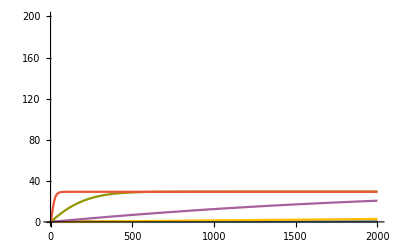

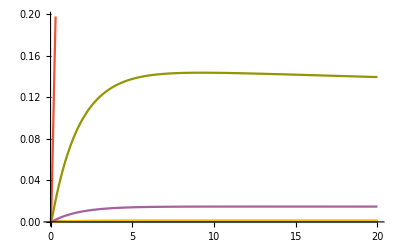

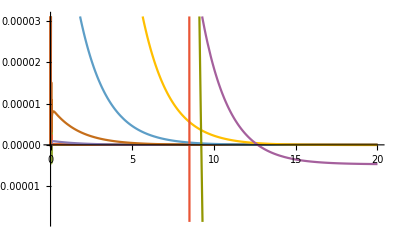

```mathematica
(*degRate =1*)
getProduct[viralLoad_, degRate_] :=  Subscript[c, product]/.NDSolve[toSolve/.Thread[{targetInitial, cleavageRate} -> {viralLoad, degRate}], {Subscript[c, a4],Subscript[c, a4u6],Subscript[c, cas13],Subscript[c, cleavageRate],Subscript[c, csm6],Subscript[c, csm6Active],Subscript[c, csm6ActiveReporter],Subscript[c, guide],Subscript[c, product],Subscript[c, reporter],Subscript[c, rnp],Subscript[c, rnpa4u6],Subscript[c, rnpActive],Subscript[c, rnpActivea4u6],Subscript[c, target]},{t, 0, 2000},MaxStepSize -> 0.001]
viralSweep = {b,{0,10^-9,10^-8, 10^-7, 10^-6, 10^-5, 10^-4 ,10^-3,10^-2,10^-1,10^0}}
resultTable=Evaluate@Table[getProduct[b,1],Evaluate@viralSweep]
Plot[Evaluate@Map[Function[x,x[t]],resultTable, {2}],{t, 0, 2000}, PlotRange->{0,200}]
Plot[Evaluate@Map[Function[x,x'[t]],resultTable, {2}],{t, 0, 20}]
Plot[Evaluate@Map[Function[x,x''[t]],resultTable, {2}],{t, 0, 20}]
```

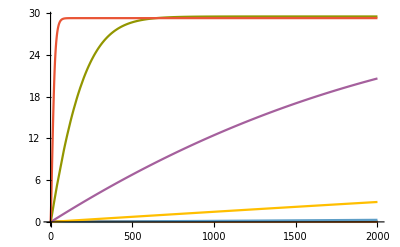

```mathematica
Plot[Evaluate@Map[Function[x,x[t]],resultTable, {2}],{t, 0, 2000}]
```

```mathematica
Map[Function[y, FindMaxValue[y,t]],Map[Function[x,x'[t]],resultTable, {2}]]
Map[Function[y, FindMaxValue[y,t]],Map[Function[x,x''[t]],resultTable, {2}]]
```

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

InterpolatingFunction::dmval: Input value {-199.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaxValue::lstol will be suppressed during this calculation.

{1.43909×10^-7,1.45389×10^-7,1.58713×10^-7,2.91947×10^-7,1.62429×10^-6,0.0000149476,0.000148173,0.00147973,0.0147417,0.143452,1.0468}

InterpolatingFunction::dmval: Input value {-19.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaxValue::sdprec: Line search unable to find a sufficient increase in the function value with MachinePrecision digit precision.

General::stop: Further output of FindMaxValue::sdprec will be suppressed during this calculation.

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaxValue::lstol will be suppressed during this calculation.

{7.29097×10^-6,7.24494×10^-6,2.34575×10^-6,2.07704×10^-6,8.80457×10^-7,8.11288×10^-6,0.000080437,0.000803635,0.00803138,0.0798888,0.759767}

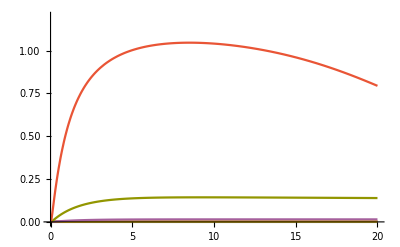

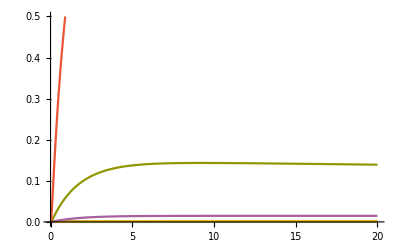

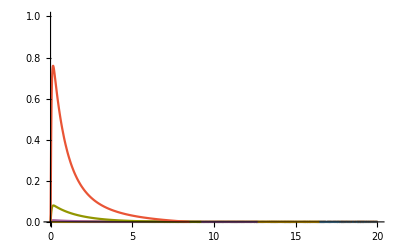

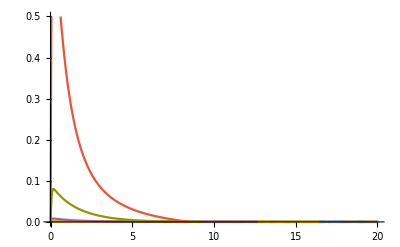

```mathematica
Plot[Evaluate@Map[Function[x,x'[t]],resultTable, {2}],{t, 0, 20}, PlotRange->{0,1.2}]
Plot[Evaluate@Map[Function[x,x'[t]],resultTable, {2}],{t, 0, 20}, PlotRange->{0,0.5}]
Plot[Evaluate@Map[Function[x,x''[t]],resultTable, {2}],{t, 0, 20}, PlotRange->{0,1}]
Plot[Evaluate@Map[Function[x,x''[t]],resultTable, {2}],{t, 0, 20}, PlotRange->{0,0.5}]
```

{b,{0,1/1000000000,1/100000000,1/10000000,1/1000000,1/100000,1/10000,1/1000,1/100,1/10,1}}

{{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]}}

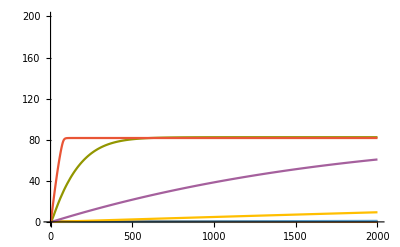

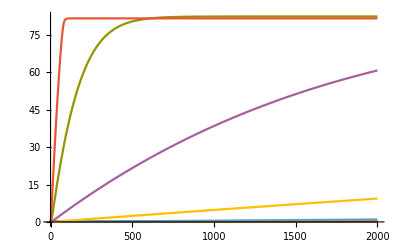

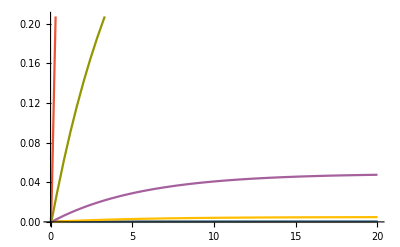

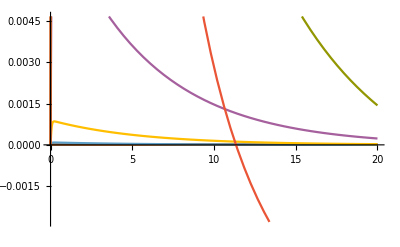

InterpolatingFunction::dmval: Input value {-2179.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaxValue::lstol will be suppressed during this calculation.

{4.79697×10^-7,4.84632×10^-7,5.29036×10^-7,9.63839×10^-7,5.41425×10^-6,0.0000498201,0.000493469,0.00492373,0.0485125,0.435118,1.28259}

InterpolatingFunction::dmval: Input value {-19.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaxValue::lstol will be suppressed during this calculation.

{8.2141×10^-8,8.29919×10^-8,9.06542×10^-8,1.67382×10^-7,9.35007×10^-7,8.61141×10^-6,0.0000853749,0.000852945,0.00852225,0.0845919,0.793453}

```mathematica
(*degRate =0.3*)
getProduct[viralLoad_, degRate_] :=  Subscript[c, product]/.NDSolve[toSolve/.Thread[{targetInitial, cleavageRate} -> {viralLoad, degRate}], {Subscript[c, a4],Subscript[c, a4u6],Subscript[c, cas13],Subscript[c, csm6],Subscript[c, csm6Active],Subscript[c, csm6ActiveReporter],Subscript[c, guide],Subscript[c, product],Subscript[c, reporter],Subscript[c, rnp],Subscript[c, rnpa4u6],Subscript[c, rnpActive],Subscript[c, rnpActivea4u6],Subscript[c, target]},{t, 0, 2000},MaxStepSize -> 0.001]
viralSweep = {b,{0,10^-9,10^-8, 10^-7, 10^-6, 10^-5, 10^-4 ,10^-3,10^-2,10^-1,10^0}}
resultTable=Evaluate@Table[getProduct[b,0.3],Evaluate@viralSweep]
Plot[Evaluate@Map[Function[x,x[t]],resultTable, {2}],{t, 0, 2000}, PlotRange->{0,200}]
Plot[Evaluate@Map[Function[x,x[t]],resultTable, {2}],{t, 0, 2000}]
Plot[Evaluate@Map[Function[x,x'[t]],resultTable, {2}],{t, 0, 20}]
Plot[Evaluate@Map[Function[x,x''[t]],resultTable, {2}],{t, 0, 20}]
Map[Function[y, FindMaxValue[y,t]],Map[Function[x,x'[t]],resultTable, {2}]]
Map[Function[y, FindMaxValue[y,t]],Map[Function[x,x''[t]],resultTable, {2}]]
```

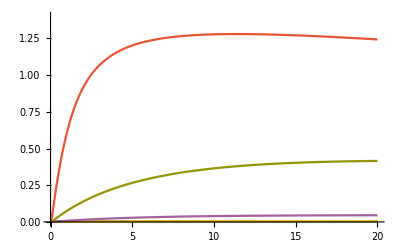

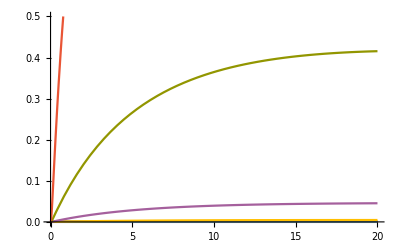

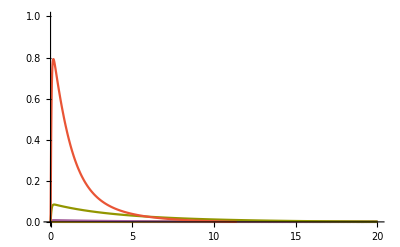

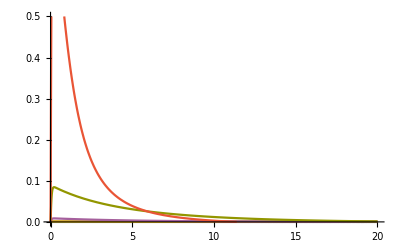

```mathematica
Plot[Evaluate@Map[Function[x,x'[t]],resultTable, {2}],{t, 0, 20}, PlotRange->{0,1.4}]
Plot[Evaluate@Map[Function[x,x'[t]],resultTable, {2}],{t, 0, 20}, PlotRange->{0,0.5}]
Plot[Evaluate@Map[Function[x,x''[t]],resultTable, {2}],{t, 0, 20}, PlotRange->{0,1}]
Plot[Evaluate@Map[Function[x,x''[t]],resultTable, {2}],{t, 0, 20}, PlotRange->{0,0.5}]
```

{b,{0,1/1000000000,1/100000000,1/10000000,1/1000000,1/100000,1/10000,1/1000,1/100,1/10,1}}

{{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]}}

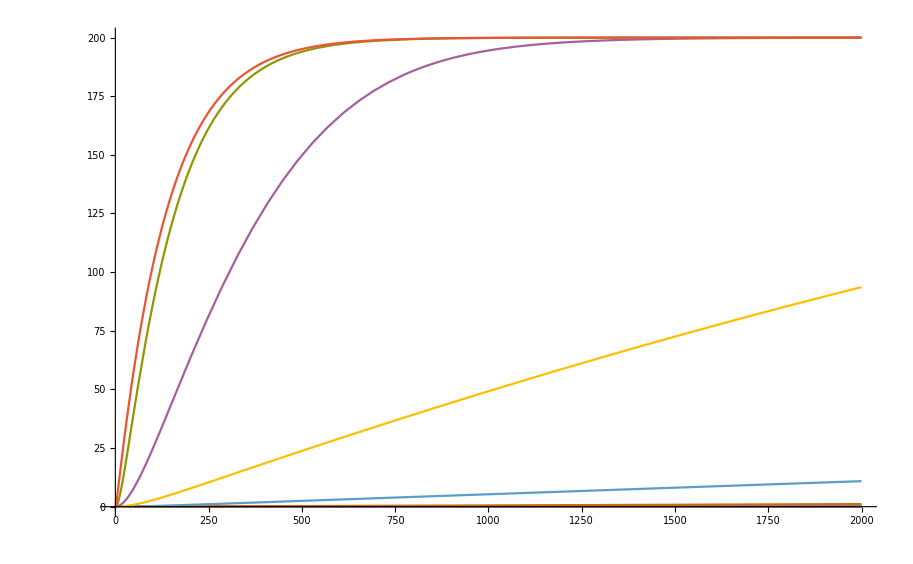

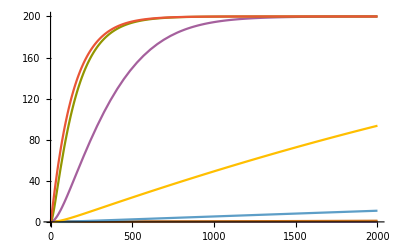

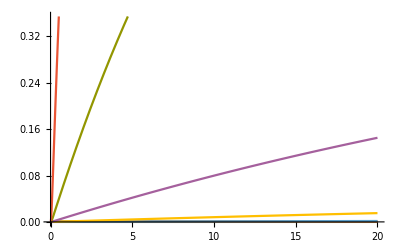

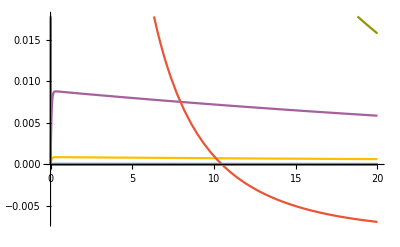

InterpolatingFunction::dmval: Input value {5579.37} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaxValue::lstol will be suppressed during this calculation.

{5.18479×10^-6,3.87214×10^-6,5.10817×10^-6,9.39582×10^-6,0.0000599594,0.000574411,0.00565844,0.0539346,0.388952,1.01074,1.31614}

InterpolatingFunction::dmval: Input value {-19.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaxValue::lstol will be suppressed during this calculation.

{8.48691×10^-8,8.57427×10^-8,9.36043×10^-8,1.72221×10^-7,9.67333×10^-7,8.90443×10^-6,0.0000882744,0.000881866,0.00880722,0.0871373,0.808475}

```mathematica
(*degRate =0.01*)
getProduct[viralLoad_, degRate_] :=  Subscript[c, product]/.NDSolve[toSolve/.Thread[{targetInitial, cleavageRate} -> {viralLoad, degRate}], {Subscript[c, a4],Subscript[c, a4u6],Subscript[c, cas13],Subscript[c, csm6],Subscript[c, csm6Active],Subscript[c, csm6ActiveReporter],Subscript[c, guide],Subscript[c, product],Subscript[c, reporter],Subscript[c, rnp],Subscript[c, rnpa4u6],Subscript[c, rnpActive],Subscript[c, rnpActivea4u6],Subscript[c, target]},{t, 0, 2000},MaxStepSize -> 0.001]
viralSweep = {b,{0,10^-9,10^-8, 10^-7, 10^-6, 10^-5, 10^-4 ,10^-3,10^-2,10^-1,10^0}}
resultTable=Evaluate@Table[getProduct[b,0.01],Evaluate@viralSweep]
Plot[Evaluate@Map[Function[x,x[t]],resultTable, {2}],{t, 0, 2000}, PlotRange->{0,200}]
Plot[Evaluate@Map[Function[x,x[t]],resultTable, {2}],{t, 0, 2000}]
Plot[Evaluate@Map[Function[x,x'[t]],resultTable, {2}],{t, 0, 20}]
Plot[Evaluate@Map[Function[x,x''[t]],resultTable, {2}],{t, 0, 20}]
Map[Function[y, FindMaxValue[y,t]],Map[Function[x,x'[t]],resultTable, {2}]]
Map[Function[y, FindMaxValue[y,t]],Map[Function[x,x''[t]],resultTable, {2}]]
```

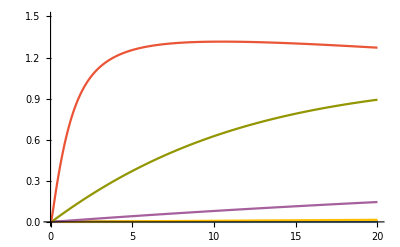

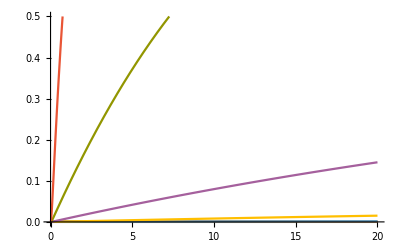

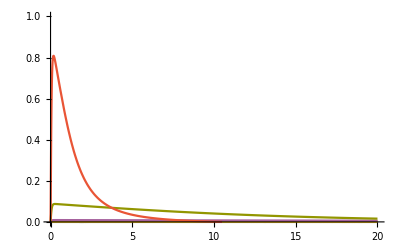

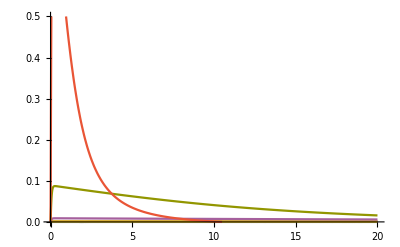

```mathematica
Plot[Evaluate@Map[Function[x,x'[t]],resultTable, {2}],{t, 0, 20}, PlotRange->{0,1.5}]
Plot[Evaluate@Map[Function[x,x'[t]],resultTable, {2}],{t, 0, 20}, PlotRange->{0,0.5}]
Plot[Evaluate@Map[Function[x,x''[t]],resultTable, {2}],{t, 0, 20}, PlotRange->{0,1}]
Plot[Evaluate@Map[Function[x,x''[t]],resultTable, {2}],{t, 0, 20}, PlotRange->{0,0.5}]
```

{b,{0,1/1000000000,1/100000000,1/10000000,1/1000000,1/100000,1/10000,1/1000,1/100,1/10,1}}

{{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]}}

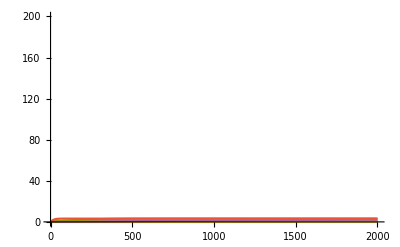

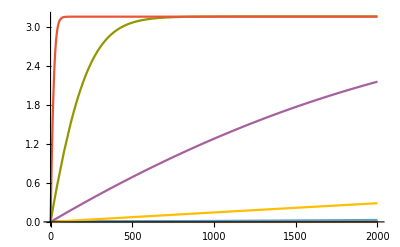

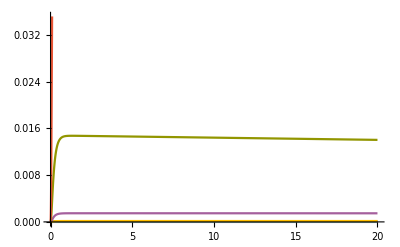

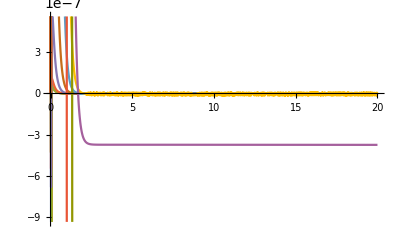

InterpolatingFunction::dmval: Input value {-198.679} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaxValue::lstol will be suppressed during this calculation.

{1.43329×10^-8,1.44803×10^-8,1.58067×10^-8,2.90702×10^-8,1.61706×10^-7,1.49238×10^-6,0.0000147939,0.000147739,0.00147739,0.0147295,0.143954}

InterpolatingFunction::dmval: Input value {-19.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaxValue::sdprec: Line search unable to find a sufficient increase in the function value with MachinePrecision digit precision.

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaxValue::lstol will be suppressed during this calculation.

{2.1804×10^-10,2.20717×10^-10,2.4481×10^-10,4.85744×10^-10,6.86366×10^-7,5.56758×10^-6,0.0000552182,0.000551713,0.00551564,0.055049,0.}

```mathematica
(*degRate =10*)
getProduct[viralLoad_, degRate_] :=  Subscript[c, product]/.NDSolve[toSolve/.Thread[{targetInitial, cleavageRate} -> {viralLoad, degRate}], {Subscript[c, a4],Subscript[c, a4u6],Subscript[c, cas13],Subscript[c, csm6],Subscript[c, csm6Active],Subscript[c, csm6ActiveReporter],Subscript[c, guide],Subscript[c, product],Subscript[c, reporter],Subscript[c, rnp],Subscript[c, rnpa4u6],Subscript[c, rnpActive],Subscript[c, rnpActivea4u6],Subscript[c, target]},{t, 0, 2000},MaxStepSize -> 0.001]
viralSweep = {b,{0,10^-9,10^-8, 10^-7, 10^-6, 10^-5, 10^-4 ,10^-3,10^-2,10^-1,10^0}}
resultTable=Evaluate@Table[getProduct[b,10],Evaluate@viralSweep]
Plot[Evaluate@Map[Function[x,x[t]],resultTable, {2}],{t, 0, 2000}, PlotRange->{0,200}]
Plot[Evaluate@Map[Function[x,x[t]],resultTable, {2}],{t, 0, 2000}]
Plot[Evaluate@Map[Function[x,x'[t]],resultTable, {2}],{t, 0, 20}]
Plot[Evaluate@Map[Function[x,x''[t]],resultTable, {2}],{t, 0, 20}]
Map[Function[y, FindMaxValue[y,t]],Map[Function[x,x'[t]],resultTable, {2}]]
Map[Function[y, FindMaxValue[y,t]],Map[Function[x,x''[t]],resultTable, {2}]]
```

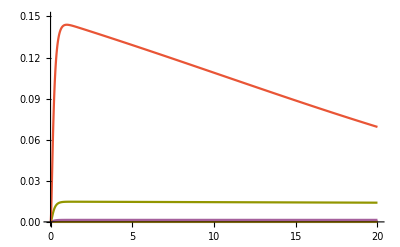

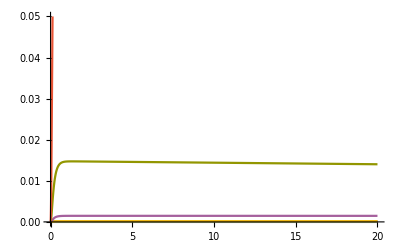

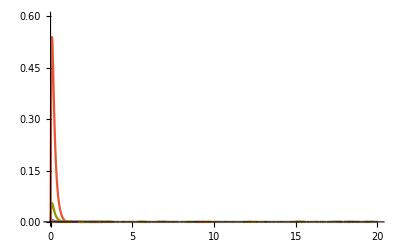

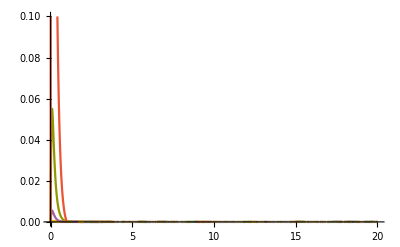

```mathematica
Plot[Evaluate@Map[Function[x,x'[t]],resultTable, {2}],{t, 0, 20}, PlotRange->{0,0.15}]
Plot[Evaluate@Map[Function[x,x'[t]],resultTable, {2}],{t, 0, 20}, PlotRange->{0,0.05}]
Plot[Evaluate@Map[Function[x,x''[t]],resultTable, {2}],{t, 0, 20}, PlotRange->{0,0.6}]
Plot[Evaluate@Map[Function[x,x''[t]],resultTable, {2}],{t, 0, 20}, PlotRange->{0,0.1}]
```

{b,{0,1/1000000000,1/100000000,1/10000000,1/1000000,1/100000,1/10000,1/1000,1/100,1/10,1}}

{{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]}}

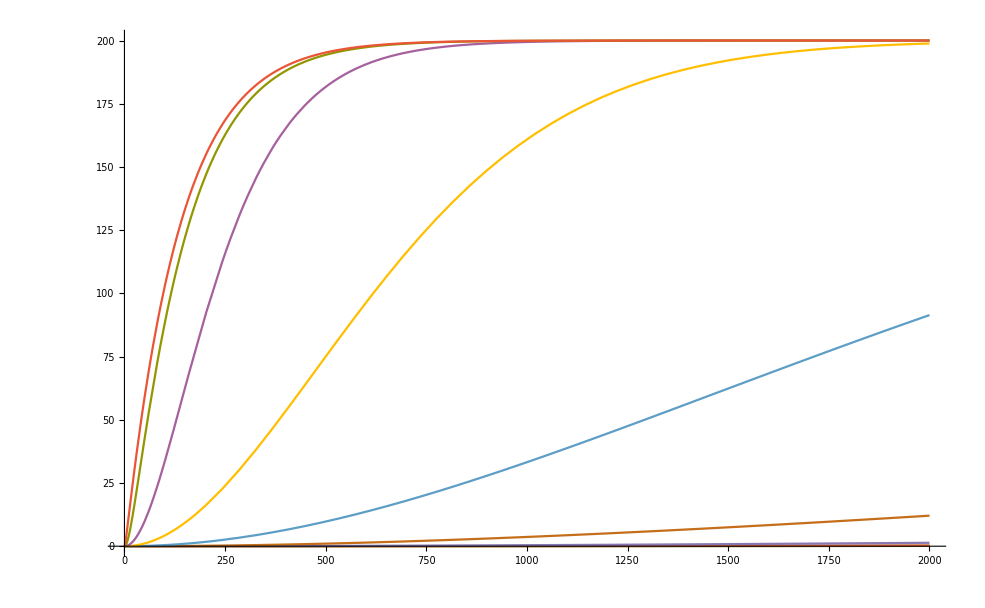

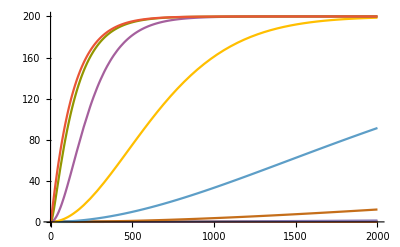

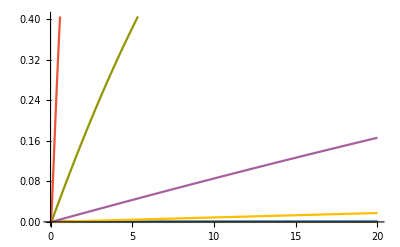

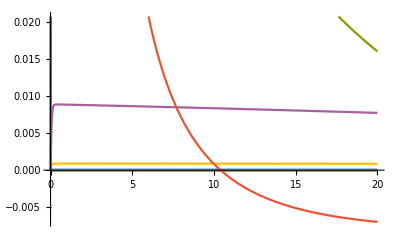

InterpolatingFunction::dmval: Input value {2661.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMaxValue::sdprec: Line search unable to find a sufficient increase in the function value with MachinePrecision digit precision.

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaxValue::lstol will be suppressed during this calculation.

{0.000099859,1706.4,0.000104728,0.000203382,0.00112613,556.388,0.0596717,0.217826,0.588548,1.043,1.31844}

InterpolatingFunction::dmval: Input value {-19.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaxValue::lstol will be suppressed during this calculation.

{8.61228×10^-8,8.70088×10^-8,9.49824×10^-8,1.74719×10^-7,9.72085×10^-7,8.9457×10^-6,0.0000887035,0.000886095,0.00884617,0.0874303,0.809996}

```mathematica
(*degRate =0.001*)
getProduct[viralLoad_, degRate_] :=  Subscript[c, product]/.NDSolve[toSolve/.Thread[{targetInitial, cleavageRate} -> {viralLoad, degRate}], {Subscript[c, a4],Subscript[c, a4u6],Subscript[c, cas13],Subscript[c, csm6],Subscript[c, csm6Active],Subscript[c, csm6ActiveReporter],Subscript[c, guide],Subscript[c, product],Subscript[c, reporter],Subscript[c, rnp],Subscript[c, rnpa4u6],Subscript[c, rnpActive],Subscript[c, rnpActivea4u6],Subscript[c, target]},{t, 0, 2000},MaxStepSize -> 0.001]
viralSweep = {b,{0,10^-9,10^-8, 10^-7, 10^-6, 10^-5, 10^-4 ,10^-3,10^-2,10^-1,10^0}}
resultTable=Evaluate@Table[getProduct[b,0.001],Evaluate@viralSweep]
Plot[Evaluate@Map[Function[x,x[t]],resultTable, {2}],{t, 0, 2000}, PlotRange->{0,200}]
Plot[Evaluate@Map[Function[x,x[t]],resultTable, {2}],{t, 0, 2000}]
Plot[Evaluate@Map[Function[x,x'[t]],resultTable, {2}],{t, 0, 20}]
Plot[Evaluate@Map[Function[x,x''[t]],resultTable, {2}],{t, 0, 20}]
Map[Function[y, FindMaxValue[y,t]],Map[Function[x,x'[t]],resultTable, {2}]]
Map[Function[y, FindMaxValue[y,t]],Map[Function[x,x''[t]],resultTable, {2}]]
```

{b,{0,1/1000000000,1/100000000,1/10000000,1/1000000,1/100000,1/10000,1/1000,1/100,1/10,1}}

{{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]}}

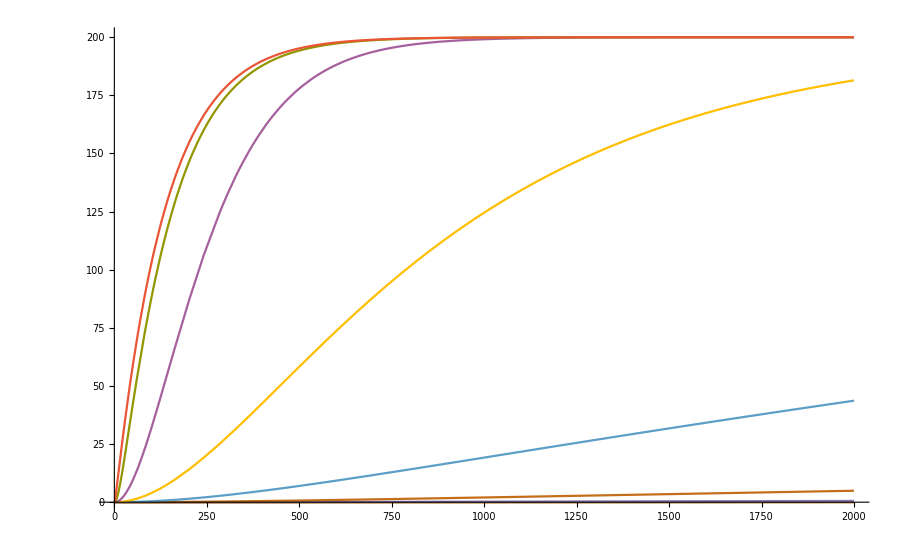

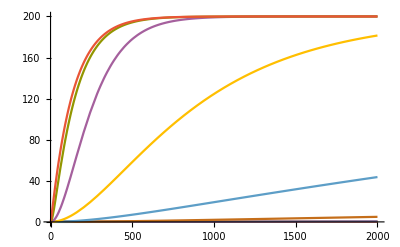

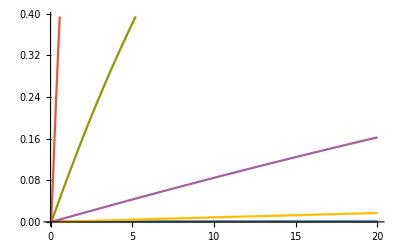

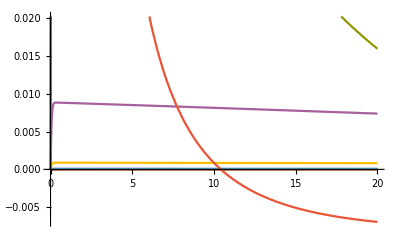

InterpolatingFunction::dmval: Input value {2661.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMaxValue::sdprec: Line search unable to find a sufficient increase in the function value with MachinePrecision digit precision.

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaxValue::lstol will be suppressed during this calculation.

{0.0000147932,0.0000276051,0.0000240996,0.0000582061,0.000304904,2.96934×10^12,0.0253902,0.157564,0.553086,1.0379,1.31807}

InterpolatingFunction::dmval: Input value {-19.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaxValue::lstol will be suppressed during this calculation.

{8.59223×10^-8,8.68062×10^-8,9.4762×10^-8,1.74319×10^-7,9.69894×10^-7,8.93969×10^-6,0.0000886221,0.00088531,0.00883947,0.0873837,0.809765}

```mathematica
(*degRate =0.005*)
getProduct[viralLoad_, degRate_] :=  Subscript[c, product]/.NDSolve[toSolve/.Thread[{targetInitial, cleavageRate} -> {viralLoad, degRate}], {Subscript[c, a4],Subscript[c, a4u6],Subscript[c, cas13],Subscript[c, csm6],Subscript[c, csm6Active],Subscript[c, csm6ActiveReporter],Subscript[c, guide],Subscript[c, product],Subscript[c, reporter],Subscript[c, rnp],Subscript[c, rnpa4u6],Subscript[c, rnpActive],Subscript[c, rnpActivea4u6],Subscript[c, target]},{t, 0, 2000},MaxStepSize -> 0.001]
viralSweep = {b,{0,10^-9,10^-8, 10^-7, 10^-6, 10^-5, 10^-4 ,10^-3,10^-2,10^-1,10^0}}
resultTable=Evaluate@Table[getProduct[b,0.005],Evaluate@viralSweep]
Plot[Evaluate@Map[Function[x,x[t]],resultTable, {2}],{t, 0, 2000}, PlotRange->{0,200}]
Plot[Evaluate@Map[Function[x,x[t]],resultTable, {2}],{t, 0, 2000}]
Plot[Evaluate@Map[Function[x,x'[t]],resultTable, {2}],{t, 0, 20}]
Plot[Evaluate@Map[Function[x,x''[t]],resultTable, {2}],{t, 0, 20}]
Map[Function[y, FindMaxValue[y,t]],Map[Function[x,x'[t]],resultTable, {2}]]
Map[Function[y, FindMaxValue[y,t]],Map[Function[x,x''[t]],resultTable, {2}]]
```

{b,{0,1/1000000000,1/100000000,1/10000000,1/1000000,1/100000,1/10000,1/1000,1/100,1/10,1}}

{{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]}}

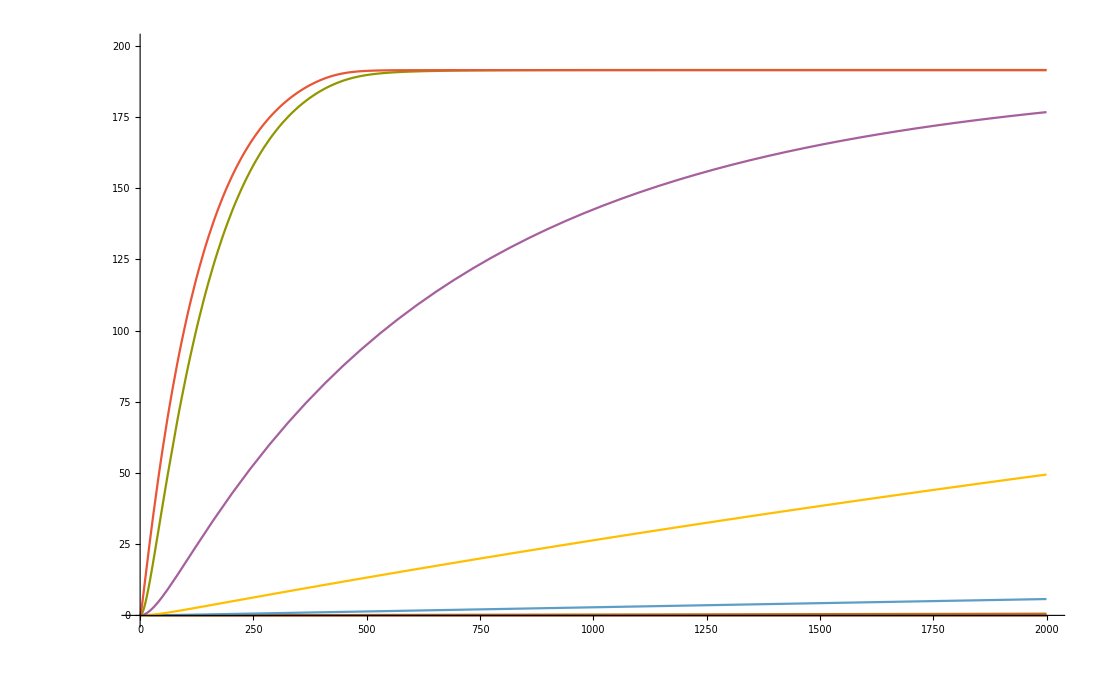

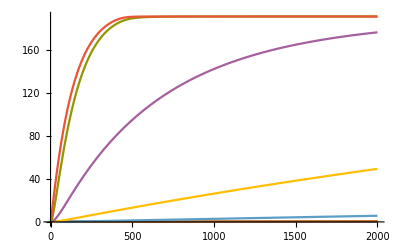

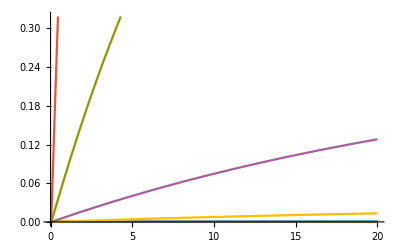

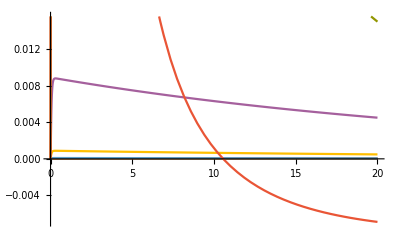

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

InterpolatingFunction::dmval: Input value {2761.48} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaxValue::lstol will be suppressed during this calculation.

{2.85335×10^-6,2.87571×10^-6,2.95654×10^-6,5.30506×10^-6,0.0000324346,9423.34,0.00295082,0.0287266,0.245581,0.967598,1.31374}

InterpolatingFunction::dmval: Input value {-19.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaxValue::lstol will be suppressed during this calculation.

{8.36977×10^-8,8.45595×10^-8,9.23165×10^-8,1.69886×10^-7,9.63691×10^-7,8.87177×10^-6,0.0000879517,0.000878654,0.00877616,0.0868848,0.807175}

```mathematica
(*degRate =0.05*)
getProduct[viralLoad_, degRate_] :=  Subscript[c, product]/.NDSolve[toSolve/.Thread[{targetInitial, cleavageRate} -> {viralLoad, degRate}], {Subscript[c, a4],Subscript[c, a4u6],Subscript[c, cas13],Subscript[c, csm6],Subscript[c, csm6Active],Subscript[c, csm6ActiveReporter],Subscript[c, guide],Subscript[c, product],Subscript[c, reporter],Subscript[c, rnp],Subscript[c, rnpa4u6],Subscript[c, rnpActive],Subscript[c, rnpActivea4u6],Subscript[c, target]},{t, 0, 2000},MaxStepSize -> 0.001]
viralSweep = {b,{0,10^-9,10^-8, 10^-7, 10^-6, 10^-5, 10^-4 ,10^-3,10^-2,10^-1,10^0}}
resultTable=Evaluate@Table[getProduct[b,0.05],Evaluate@viralSweep]
Plot[Evaluate@Map[Function[x,x[t]],resultTable, {2}],{t, 0, 2000}, PlotRange->{0,200}]
Plot[Evaluate@Map[Function[x,x[t]],resultTable, {2}],{t, 0, 2000}]
Plot[Evaluate@Map[Function[x,x'[t]],resultTable, {2}],{t, 0, 20}]
Plot[Evaluate@Map[Function[x,x''[t]],resultTable, {2}],{t, 0, 20}]
Map[Function[y, FindMaxValue[y,t]],Map[Function[x,x'[t]],resultTable, {2}]]
Map[Function[y, FindMaxValue[y,t]],Map[Function[x,x''[t]],resultTable, {2}]]
```

{b,{0,1/1000000000,1/100000000,1/10000000,1/1000000,1/100000,1/10000,1/1000,1/100,1/10,1}}

{{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]}}

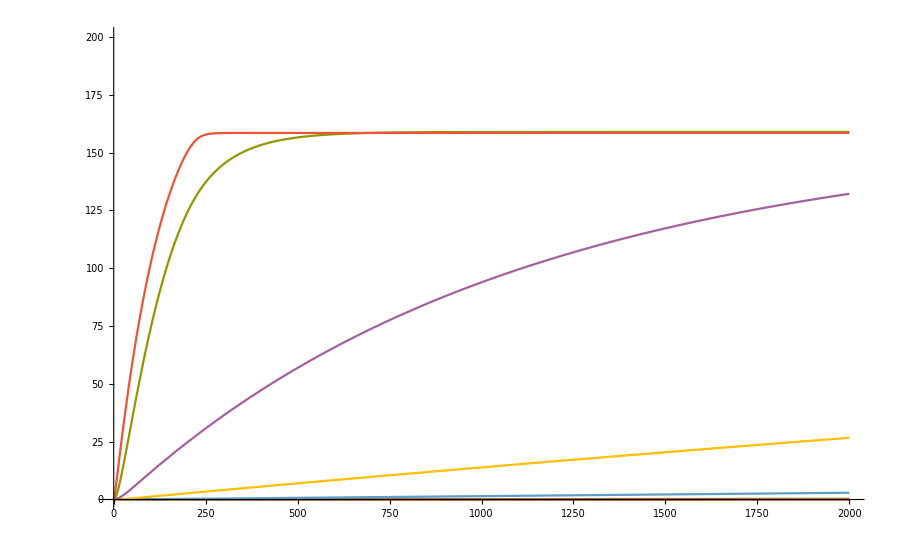

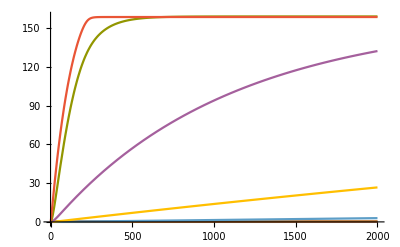

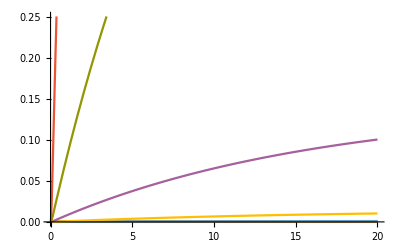

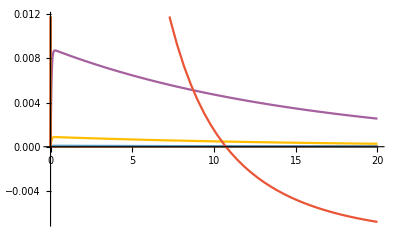

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaxValue::lstol will be suppressed during this calculation.

```mathematica
(*degRate =0.1*)
getProduct[viralLoad_, degRate_] :=  Subscript[c, product]/.NDSolve[toSolve/.Thread[{targetInitial, cleavageRate} -> {viralLoad, degRate}], {Subscript[c, a4],Subscript[c, a4u6],Subscript[c, cas13],Subscript[c, csm6],Subscript[c, csm6Active],Subscript[c, csm6ActiveReporter],Subscript[c, guide],Subscript[c, product],Subscript[c, reporter],Subscript[c, rnp],Subscript[c, rnpa4u6],Subscript[c, rnpActive],Subscript[c, rnpActivea4u6],Subscript[c, target]},{t, 0, 2000},MaxStepSize -> 0.001]
viralSweep = {b,{0,10^-9,10^-8, 10^-7, 10^-6, 10^-5, 10^-4 ,10^-3,10^-2,10^-1,10^0}}
resultTable=Evaluate@Table[getProduct[b,0.1],Evaluate@viralSweep]
Plot[Evaluate@Map[Function[x,x[t]],resultTable, {2}],{t, 0, 2000}, PlotRange->{0,200}]
Plot[Evaluate@Map[Function[x,x[t]],resultTable, {2}],{t, 0, 2000}]
Plot[Evaluate@Map[Function[x,x'[t]],resultTable, {2}],{t, 0, 20}]
Plot[Evaluate@Map[Function[x,x''[t]],resultTable, {2}],{t, 0, 20}]
Map[Function[y, FindMaxValue[y,t]],Map[Function[x,x'[t]],resultTable, {2}]]
Map[Function[y, FindMaxValue[y,t]],Map[Function[x,x''[t]],resultTable, {2}]]
```

```mathematica
{1.4369055422387273*^-6,1.4504408357505717*^-6,1.587127777198038*^-6,2.919466027205963*^-6,0.000016239433293639214,0.0001494501490730458,0.0014796777123513097,


46469,0.13762917367138133,0.8538520089979459,1.308553934607172}
```

InterpolatingFunction::dmval: Input value {-19.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaxValue::lstol will be suppressed during this calculation.

{8.12927×10^-8,8.21307×10^-8,8.96725×10^-8,1.65091×10^-7,9.56892×10^-7,8.81036×10^-6,0.0000873442,0.000872598,0.0087168,0.0863728,0.804343}

{b,{0,1/1000000000,1/100000000,1/10000000,1/1000000,1/100000,1/10000,1/1000,1/100,1/10,1}}

{{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]}}

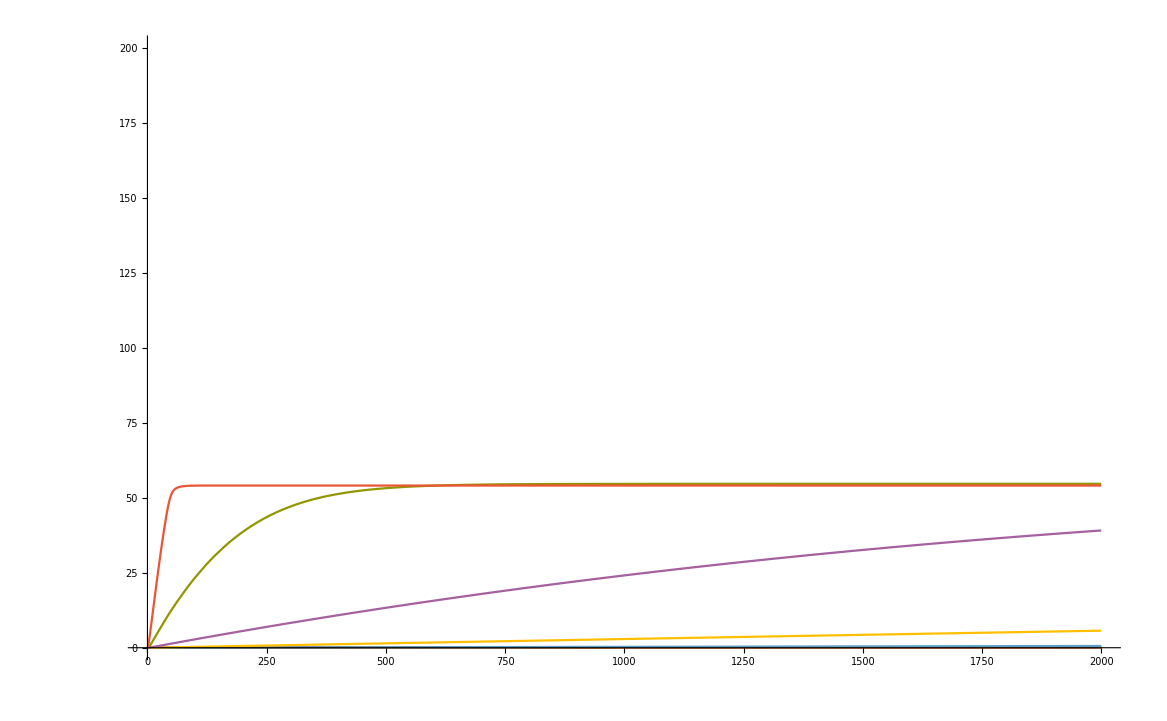

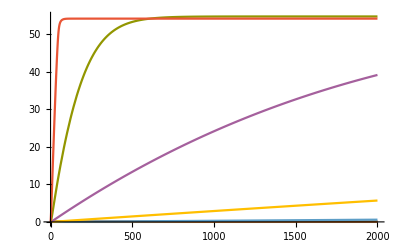

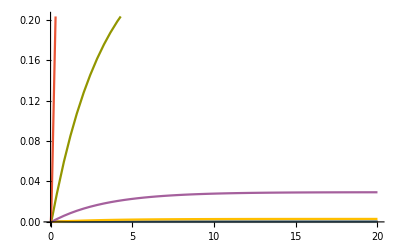

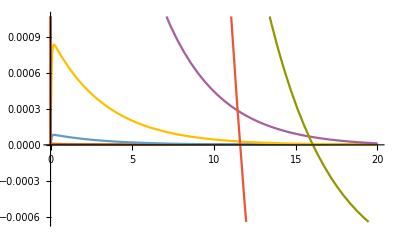

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

InterpolatingFunction::dmval: Input value {-2183.37} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaxValue::lstol will be suppressed during this calculation.

{2.87313×10^-7,2.90779×10^-7,3.16839×10^-7,5.82867×10^-7,3.24856×10^-6,0.0000298927,0.000296091,0.00295664,0.0293377,0.276712,1.24351}

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

InterpolatingFunction::dmval: Input value {-19.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaxValue::lstol will be suppressed during this calculation.

{8.06227×10^-8,8.14489×10^-8,8.89121×10^-8,1.64067×10^-7,9.17079×10^-7,8.44783×10^-6,0.0000837549,0.00083677,0.00836146,0.0830699,0.783187}

```mathematica
(*degRate =0.5*)
getProduct[viralLoad_, degRate_] :=  Subscript[c, product]/.NDSolve[toSolve/.Thread[{targetInitial, cleavageRate} -> {viralLoad, degRate}], {Subscript[c, a4],Subscript[c, a4u6],Subscript[c, cas13],Subscript[c, csm6],Subscript[c, csm6Active],Subscript[c, csm6ActiveReporter],Subscript[c, guide],Subscript[c, product],Subscript[c, reporter],Subscript[c, rnp],Subscript[c, rnpa4u6],Subscript[c, rnpActive],Subscript[c, rnpActivea4u6],Subscript[c, target]},{t, 0, 2000},MaxStepSize -> 0.001]
viralSweep = {b,{0,10^-9,10^-8, 10^-7, 10^-6, 10^-5, 10^-4 ,10^-3,10^-2,10^-1,10^0}}
resultTable=Evaluate@Table[getProduct[b,0.5],Evaluate@viralSweep]
Plot[Evaluate@Map[Function[x,x[t]],resultTable, {2}],{t, 0, 2000}, PlotRange->{0,200}]
Plot[Evaluate@Map[Function[x,x[t]],resultTable, {2}],{t, 0, 2000}]
Plot[Evaluate@Map[Function[x,x'[t]],resultTable, {2}],{t, 0, 20}]
Plot[Evaluate@Map[Function[x,x''[t]],resultTable, {2}],{t, 0, 20}]
Map[Function[y, FindMaxValue[y,t]],Map[Function[x,x'[t]],resultTable, {2}]]
Map[Function[y, FindMaxValue[y,t]],Map[Function[x,x''[t]],resultTable, {2}]]
```

```mathematica
(*CSM6 activator sweep*)
```

```mathematica
(*rates of stuff*)
cas13Binding = 1;
cas13DissocGuide = 5;
cas13DissocSubs = 2000;
cas13DissocTarget = 1;
cas13Clevage = 200;
cas13Background = cas13Clevage/(5*10^8);
csm6ActivatorBinding = 1;
csm6ActivatorUnbinding = 63; (*Km from tina turn into kd at some point*)
csm6Kcat = 0.4;
csm6SubstrateBinding = 1;
csm6SubstrateUnbinding = 5000;(*Kd? from tina turn maybe its a Km*)
csm6SubstrateUnbinding
```

5000

```mathematica
(*concentrations*)
reporterInitial = 200;
cas13Initial = 50;
guideInitial = 50;
rnpInitial = 0;
csm6Initial = 100;
csm6Initial
```

100

```mathematica
csm6ActivatorCleavage= cleavageRate;
onTargetCas13 = {{cas13 + guide ⇌ rnp, {cas13Binding, cas13DissocTarget}},
{rnp + target ⇌ rnpActive, {cas13Binding, cas13DissocTarget}},
{rnpActive + a4u6 ⇌ rnpActivea4u6, {cas13Binding, cas13DissocSubs}},
{rnpActivea4u6 -> rnpActive + a4, {cas13Clevage}}
};
backgroundCas13 = {{rnp +a4u6 ⇌ rnpa4u6, {cas13Binding, cas13DissocSubs}},
{rnpa4u6 -> rnp + a4, {cas13Background}}
};
csm6Reactions = {{csm6 + a4 ⇌ csm6Active, {csm6ActivatorBinding, csm6ActivatorUnbinding-csm6ActivatorCleavage}},
{csm6Active -> csm6, {csm6ActivatorCleavage}},
{csm6Active + reporter ⇌ csm6ActiveReporter, {csm6SubstrateBinding, csm6SubstrateUnbinding}},
{csm6ActiveReporter -> csm6Active +product, {csm6Kcat}}
};

rxns = Join[onTargetCas13, backgroundCas13, csm6Reactions]
Dimensions[rxns]
eqs = rxns[[All,1]]
DescriptiveRK[eqs]
rates = Flatten[rxns[[All,2]]]
```

{{cas13+guide⇌rnp,{1,1}},{rnp+target⇌rnpActive,{1,1}},{a4u6+rnpActive⇌rnpActivea4u6,{1,2000}},{rnpActivea4u6→a4+rnpActive,{200}},{a4u6+rnp⇌rnpa4u6,{1,2000}},{rnpa4u6→a4+rnp,{1/2500000}},{a4+csm6⇌csm6Active,{1,63-cleavageRate}},{csm6Active→csm6,{cleavageRate}},{csm6Active+reporter⇌csm6ActiveReporter,{1,5000}},{csm6ActiveReporter→csm6Active+product,{0.4}}}

{10,2}

{cas13+guide⇌rnp,rnp+target⇌rnpActive,a4u6+rnpActive⇌rnpActivea4u6,rnpActivea4u6→a4+rnpActive,a4u6+rnp⇌rnpa4u6,rnpa4u6→a4+rnp,a4+csm6⇌csm6Active,csm6Active→csm6,csm6Active+reporter⇌csm6ActiveReporter,csm6ActiveReporter→csm6Active+product}

{a4,a4u6,cas13,csm6,csm6Active,csm6ActiveReporter,guide,product,reporter,rnp,rnpa4u6,rnpActive,rnpActivea4u6,target}

{c_a4[t],c_a4u6[t],c_cas13[t],c_csm6[t],c_csm6Active[t],c_csm6ActiveReporter[t],c_guide[t],c_product[t],c_reporter[t],c_rnp[t],c_rnpa4u6[t],c_rnpActive[t],c_rnpActivea4u6[t],c_target[t]}

{c_a4,c_a4u6,c_cas13,c_csm6,c_csm6Active,c_csm6ActiveReporter,c_guide,c_product,c_reporter,c_rnp,c_rnpa4u6,c_rnpActive,c_rnpActivea4u6,c_target}

{c_a4[0]==0,c_a4u6[0]==0,c_cas13[0]==0,c_csm6[0]==0,c_csm6Active[0]==0,c_csm6ActiveReporter[0]==0,c_guide[0]==0,c_product[0]==0,c_reporter[0]==0,c_rnp[0]==0,c_rnpa4u6[0]==0,c_rnpActive[0]==0,c_rnpActivea4u6[0]==0,c_target[0]==0}

{k_1,k_2,k_3,k_4,k_5,k_6,k_7,k_8,k_9,k_10,k_11,k_12,k_13,k_14,k_15,k_16}

{c_a4'[t]==-k_11 c_a4[t] c_csm6[t]+k_12 c_csm6Active[t]+k_10 c_rnpa4u6[t]+k_7 c_rnpActivea4u6[t],c_a4u6'[t]==-k_8 c_a4u6[t] c_rnp[t]+k_9 c_rnpa4u6[t]-k_5 c_a4u6[t] c_rnpActive[t]+k_6 c_rnpActivea4u6[t],c_cas13'[t]==-k_1 c_cas13[t] c_guide[t]+k_2 c_rnp[t],c_csm6'[t]==-k_11 c_a4[t] c_csm6[t]+k_12 c_csm6Active[t]+k_13 c_csm6Active[t],c_csm6Active'[t]==k_11 c_a4[t] c_csm6[t]-k_12 c_csm6Active[t]-k_13 c_csm6Active[t]+k_15 c_csm6ActiveReporter[t]+k_16 c_csm6ActiveReporter[t]-k_14 c_csm6Active[t] c_reporter[t],c_csm6ActiveReporter'[t]==-k_15 c_csm6ActiveReporter[t]-k_16 c_csm6ActiveReporter[t]+k_14 c_csm6Active[t] c_reporter[t],c_guide'[t]==-k_1 c_cas13[t] c_guide[t]+k_2 c_rnp[t],c_product'[t]==k_16 c_csm6ActiveReporter[t],c_reporter'[t]==k_15 c_csm6ActiveReporter[t]-k_14 c_csm6Active[t] c_reporter[t],c_rnp'[t]==k_1 c_cas13[t] c_guide[t]-k_2 c_rnp[t]-k_8 c_a4u6[t] c_rnp[t]+k_9 c_rnpa4u6[t]+k_10 c_rnpa4u6[t]+k_4 c_rnpActive[t]-k_3 c_rnp[t] c_target[t],c_rnpa4u6'[t]==k_8 c_a4u6[t] c_rnp[t]-k_9 c_rnpa4u6[t]-k_10 c_rnpa4u6[t],c_rnpActive'[t]==-k_4 c_rnpActive[t]-k_5 c_a4u6[t] c_rnpActive[t]+k_6 c_rnpActivea4u6[t]+k_7 c_rnpActivea4u6[t]+k_3 c_rnp[t] c_target[t],c_rnpActivea4u6'[t]==k_5 c_a4u6[t] c_rnpActive[t]-k_6 c_rnpActivea4u6[t]-k_7 c_rnpActivea4u6[t],c_target'[t]==k_4 c_rnpActive[t]-k_3 c_rnp[t] c_target[t]}

complex chemical reaction | {cas13+guide→rnp,rnp→cas13+guide,rnp+target→rnpActive,rnpActive→rnp+target,a4u6+rnpActive→rnpActivea4u6,rnpActivea4u6→a4u6+rnpActive,rnpActivea4u6→a4+rnpActive,a4u6+rnp→rnpa4u6,rnpa4u6→a4u6+rnp,rnpa4u6→a4+rnp,a4+csm6→csm6Active,csm6Active→a4+csm6,csm6Active→csm6,csm6Active+reporter→csm6ActiveReporter,csm6ActiveReporter→csm6Active+reporter,csm6ActiveReporter→csm6Active+product}
number of reaction steps | 16
chemical species | {a4,a4u6,cas13,csm6,csm6Active,csm6ActiveReporter,guide,product,reporter,rnp,rnpa4u6,rnpActive,rnpActivea4u6,target}
number of chemical species | 14
external species | {}
number of external species | 0
complexes | {csm6,a4+csm6,csm6Active,csm6ActiveReporter,cas13+guide,csm6Active+product,csm6Active+reporter,rnp,a4+rnp,a4u6+rnp,rnpa4u6,rnpActive,a4+rnpActive,a4u6+rnpActive,rnpActivea4u6,rnp+target}
number of complexes | 16
matrix of reactant
complex vectors (α) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
matrix of product
complex vectors (β) | (0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
stoichiometric matrix (γ) | (0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | -1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 1 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | -1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1
-1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0
1 | -1 | -1 | 1 | 0 | 0 | 0 | -1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | -1 | -1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
induced mass action kinetic
differential equations
(CCD model) | c_a4'[t]==-k_11 c_a4[t] c_csm6[t]+k_12 c_csm6Active[t]+k_10 c_rnpa4u6[t]+k_7 c_rnpActivea4u6[t]
c_a4u6'[t]==-k_8 c_a4u6[t] c_rnp[t]+k_9 c_rnpa4u6[t]-k_5 c_a4u6[t] c_rnpActive[t]+k_6 c_rnpActivea4u6[t]
c_cas13'[t]==-k_1 c_cas13[t] c_guide[t]+k_2 c_rnp[t]
c_csm6'[t]==-k_11 c_a4[t] c_csm6[t]+k_12 c_csm6Active[t]+k_13 c_csm6Active[t]
c_csm6Active'[t]==k_11 c_a4[t] c_csm6[t]-k_12 c_csm6Active[t]-k_13 c_csm6Active[t]+k_15 c_csm6ActiveReporter[t]+k_16 c_csm6ActiveReporter[t]-k_14 c_csm6Active[t] c_reporter[t]
c_csm6ActiveReporter'[t]==-k_15 c_csm6ActiveReporter[t]-k_16 c_csm6ActiveReporter[t]+k_14 c_csm6Active[t] c_reporter[t]
c_guide'[t]==-k_1 c_cas13[t] c_guide[t]+k_2 c_rnp[t]
c_product'[t]==k_16 c_csm6ActiveReporter[t]
c_reporter'[t]==k_15 c_csm6ActiveReporter[t]-k_14 c_csm6Active[t] c_reporter[t]
c_rnp'[t]==k_1 c_cas13[t] c_guide[t]-k_2 c_rnp[t]-k_8 c_a4u6[t] c_rnp[t]+k_9 c_rnpa4u6[t]+k_10 c_rnpa4u6[t]+k_4 c_rnpActive[t]-k_3 c_rnp[t] c_target[t]
c_rnpa4u6'[t]==k_8 c_a4u6[t] c_rnp[t]-k_9 c_rnpa4u6[t]-k_10 c_rnpa4u6[t]
c_rnpActive'[t]==-k_4 c_rnpActive[t]-k_5 c_a4u6[t] c_rnpActive[t]+k_6 c_rnpActivea4u6[t]+k_7 c_rnpActivea4u6[t]+k_3 c_rnp[t] c_target[t]
c_rnpActivea4u6'[t]==k_5 c_a4u6[t] c_rnpActive[t]-k_6 c_rnpActivea4u6[t]-k_7 c_rnpActivea4u6[t]
c_target'[t]==k_4 c_rnpActive[t]-k_3 c_rnp[t] c_target[t]

{1,1,1,1,1,2000,200,1,2000,1/2500000,1,63-cleavageRate,cleavageRate,1,5000,0.4}

```mathematica
diffEqs = {Subscript[c, a4]'[t]==-Subscript[k, 11] Subscript[c, a4][t] Subscript[c, csm6][t]+Subscript[k, 12] Subscript[c, csm6Active][t]+Subscript[k, 10] Subscript[c, rnpa4u6][t]+Subscript[k, 7] Subscript[c, rnpActivea4u6][t],Subscript[c, a4u6]'[t]==-Subscript[k, 8] Subscript[c, a4u6][t] Subscript[c, rnp][t]+Subscript[k, 9] Subscript[c, rnpa4u6][t]-Subscript[k, 5] Subscript[c, a4u6][t] Subscript[c, rnpActive][t]+Subscript[k, 6] Subscript[c, rnpActivea4u6][t],Subscript[c, cas13]'[t]==-Subscript[k, 1] Subscript[c, cas13][t] Subscript[c, guide][t]+Subscript[k, 2] Subscript[c, rnp][t],Subscript[c, csm6]'[t]==-Subscript[k, 11] Subscript[c, a4][t] Subscript[c, csm6][t]+Subscript[k, 12] Subscript[c, csm6Active][t]+Subscript[k, 13] Subscript[c, csm6Active][t],Subscript[c, csm6Active]'[t]==Subscript[k, 11] Subscript[c, a4][t] Subscript[c, csm6][t]-Subscript[k, 12] Subscript[c, csm6Active][t]-Subscript[k, 13] Subscript[c, csm6Active][t]+Subscript[k, 15] Subscript[c, csm6ActiveReporter][t]+Subscript[k, 16] Subscript[c, csm6ActiveReporter][t]-Subscript[k, 14] Subscript[c, csm6Active][t] Subscript[c, reporter][t],Subscript[c, csm6ActiveReporter]'[t]==-Subscript[k, 15] Subscript[c, csm6ActiveReporter][t]-Subscript[k, 16] Subscript[c, csm6ActiveReporter][t]+Subscript[k, 14] Subscript[c, csm6Active][t] Subscript[c, reporter][t],Subscript[c, guide]'[t]==-Subscript[k, 1] Subscript[c, cas13][t] Subscript[c, guide][t]+Subscript[k, 2] Subscript[c, rnp][t],Subscript[c, product]'[t]==Subscript[k, 16] Subscript[c, csm6ActiveReporter][t],Subscript[c, reporter]'[t]==Subscript[k, 15] Subscript[c, csm6ActiveReporter][t]-Subscript[k, 14] Subscript[c, csm6Active][t] Subscript[c, reporter][t],Subscript[c, rnp]'[t]==Subscript[k, 1] Subscript[c, cas13][t] Subscript[c, guide][t]-Subscript[k, 2] Subscript[c, rnp][t]-Subscript[k, 8] Subscript[c, a4u6][t] Subscript[c, rnp][t]+Subscript[k, 9] Subscript[c, rnpa4u6][t]+Subscript[k, 10] Subscript[c, rnpa4u6][t]+Subscript[k, 4] Subscript[c, rnpActive][t]-Subscript[k, 3] Subscript[c, rnp][t] Subscript[c, target][t],Subscript[c, rnpa4u6]'[t]==Subscript[k, 8] Subscript[c, a4u6][t] Subscript[c, rnp][t]-Subscript[k, 9] Subscript[c, rnpa4u6][t]-Subscript[k, 10] Subscript[c, rnpa4u6][t],Subscript[c, rnpActive]'[t]==-Subscript[k, 4] Subscript[c, rnpActive][t]-Subscript[k, 5] Subscript[c, a4u6][t] Subscript[c, rnpActive][t]+Subscript[k, 6] Subscript[c, rnpActivea4u6][t]+Subscript[k, 7] Subscript[c, rnpActivea4u6][t]+Subscript[k, 3] Subscript[c, rnp][t] Subscript[c, target][t],Subscript[c, rnpActivea4u6]'[t]==Subscript[k, 5] Subscript[c, a4u6][t] Subscript[c, rnpActive][t]-Subscript[k, 6] Subscript[c, rnpActivea4u6][t]-Subscript[k, 7] Subscript[c, rnpActivea4u6][t],Subscript[c, target]'[t]==Subscript[k, 4] Subscript[c, rnpActive][t]-Subscript[k, 3] Subscript[c, rnp][t] Subscript[c, target][t]}/.Thread[{Subscript[k, 1],Subscript[k, 2],Subscript[k, 3],Subscript[k, 4],Subscript[k, 5],Subscript[k, 6],Subscript[k, 7],Subscript[k, 8],Subscript[k, 9],Subscript[k, 10],Subscript[k, 11],Subscript[k, 12],Subscript[k, 13],Subscript[k, 14],Subscript[k, 15],Subscript[k, 16]} -> rates]
initialConds = {Subscript[c, a4][0]==0,Subscript[c, a4u6][0]==a4u6Initial,Subscript[c, cas13][0]==cas13Initial,Subscript[c, csm6][0]==csm6Initial,Subscript[c, csm6Active][0]==0,Subscript[c, csm6ActiveReporter][0]==0,Subscript[c, guide][0]==guideInitial,Subscript[c, product][0]==0,Subscript[c, reporter][0]==reporterInitial,Subscript[c, rnp][0]==rnpInitial,Subscript[c, rnpa4u6][0]==0,Subscript[c, rnpActive][0]==0,Subscript[c, rnpActivea4u6][0]==0,Subscript[c, target][0]==targetInitial}
toSolve= Join[diffEqs,initialConds]
getProduct[viralLoad_,csm6AI_, degRate_] :=  Subscript[c, product]/.NDSolve[toSolve/.Thread[{targetInitial,a4u6Initial, cleavageRate} -> {viralLoad,csm6AI, degRate}], {Subscript[c, a4],Subscript[c, a4u6],Subscript[c, cas13],Subscript[c, csm6],Subscript[c, csm6Active],Subscript[c, csm6ActiveReporter],Subscript[c, guide],Subscript[c, product],Subscript[c, reporter],Subscript[c, rnp],Subscript[c, rnpa4u6],Subscript[c, rnpActive],Subscript[c, rnpActivea4u6],Subscript[c, target]},{t, 0, 2000},MaxStepSize -> 0.001]
viralSweep = {b,{0,10^-9,10^-8, 10^-7, 10^-6, 10^-5, 10^-4 ,10^-3,10^-2,10^-1,10^0}}
```

{c_a4'[t]==-c_a4[t] c_csm6[t]+(63-cleavageRate) c_csm6Active[t]+c_rnpa4u6[t]/2500000+200 c_rnpActivea4u6[t],c_a4u6'[t]==-c_a4u6[t] c_rnp[t]+2000 c_rnpa4u6[t]-c_a4u6[t] c_rnpActive[t]+2000 c_rnpActivea4u6[t],c_cas13'[t]==-c_cas13[t] c_guide[t]+c_rnp[t],c_csm6'[t]==-c_a4[t] c_csm6[t]+(63-cleavageRate) c_csm6Active[t]+cleavageRate c_csm6Active[t],c_csm6Active'[t]==c_a4[t] c_csm6[t]-(63-cleavageRate) c_csm6Active[t]-cleavageRate c_csm6Active[t]+5000.4 c_csm6ActiveReporter[t]-c_csm6Active[t] c_reporter[t],c_csm6ActiveReporter'[t]==-5000.4 c_csm6ActiveReporter[t]+c_csm6Active[t] c_reporter[t],c_guide'[t]==-c_cas13[t] c_guide[t]+c_rnp[t],c_product'[t]==0.4 c_csm6ActiveReporter[t],c_reporter'[t]==5000 c_csm6ActiveReporter[t]-c_csm6Active[t] c_reporter[t],c_rnp'[t]==c_cas13[t] c_guide[t]-c_rnp[t]-c_a4u6[t] c_rnp[t]+(5000000001 c_rnpa4u6[t])/2500000+c_rnpActive[t]-c_rnp[t] c_target[t],c_rnpa4u6'[t]==c_a4u6[t] c_rnp[t]-(5000000001 c_rnpa4u6[t])/2500000,c_rnpActive'[t]==-c_rnpActive[t]-c_a4u6[t] c_rnpActive[t]+2200 c_rnpActivea4u6[t]+c_rnp[t] c_target[t],c_rnpActivea4u6'[t]==c_a4u6[t] c_rnpActive[t]-2200 c_rnpActivea4u6[t],c_target'[t]==c_rnpActive[t]-c_rnp[t] c_target[t]}

{c_a4[0]==0,c_a4u6[0]==a4u6Initial,c_cas13[0]==50,c_csm6[0]==100,c_csm6Active[0]==0,c_csm6ActiveReporter[0]==0,c_guide[0]==50,c_product[0]==0,c_reporter[0]==200,c_rnp[0]==0,c_rnpa4u6[0]==0,c_rnpActive[0]==0,c_rnpActivea4u6[0]==0,c_target[0]==targetInitial}

{c_a4'[t]==-c_a4[t] c_csm6[t]+(63-cleavageRate) c_csm6Active[t]+c_rnpa4u6[t]/2500000+200 c_rnpActivea4u6[t],c_a4u6'[t]==-c_a4u6[t] c_rnp[t]+2000 c_rnpa4u6[t]-c_a4u6[t] c_rnpActive[t]+2000 c_rnpActivea4u6[t],c_cas13'[t]==-c_cas13[t] c_guide[t]+c_rnp[t],c_csm6'[t]==-c_a4[t] c_csm6[t]+(63-cleavageRate) c_csm6Active[t]+cleavageRate c_csm6Active[t],c_csm6Active'[t]==c_a4[t] c_csm6[t]-(63-cleavageRate) c_csm6Active[t]-cleavageRate c_csm6Active[t]+5000.4 c_csm6ActiveReporter[t]-c_csm6Active[t] c_reporter[t],c_csm6ActiveReporter'[t]==-5000.4 c_csm6ActiveReporter[t]+c_csm6Active[t] c_reporter[t],c_guide'[t]==-c_cas13[t] c_guide[t]+c_rnp[t],c_product'[t]==0.4 c_csm6ActiveReporter[t],c_reporter'[t]==5000 c_csm6ActiveReporter[t]-c_csm6Active[t] c_reporter[t],c_rnp'[t]==c_cas13[t] c_guide[t]-c_rnp[t]-c_a4u6[t] c_rnp[t]+(5000000001 c_rnpa4u6[t])/2500000+c_rnpActive[t]-c_rnp[t] c_target[t],c_rnpa4u6'[t]==c_a4u6[t] c_rnp[t]-(5000000001 c_rnpa4u6[t])/2500000,c_rnpActive'[t]==-c_rnpActive[t]-c_a4u6[t] c_rnpActive[t]+2200 c_rnpActivea4u6[t]+c_rnp[t] c_target[t],c_rnpActivea4u6'[t]==c_a4u6[t] c_rnpActive[t]-2200 c_rnpActivea4u6[t],c_target'[t]==c_rnpActive[t]-c_rnp[t] c_target[t],c_a4[0]==0,c_a4u6[0]==a4u6Initial,c_cas13[0]==50,c_csm6[0]==100,c_csm6Active[0]==0,c_csm6ActiveReporter[0]==0,c_guide[0]==50,c_product[0]==0,c_reporter[0]==200,c_rnp[0]==0,c_rnpa4u6[0]==0,c_rnpActive[0]==0,c_rnpActivea4u6[0]==0,c_target[0]==targetInitial}

{b,{0,1/1000000000,1/100000000,1/10000000,1/1000000,1/100000,1/10000,1/1000,1/100,1/10,1}}

{{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]}}

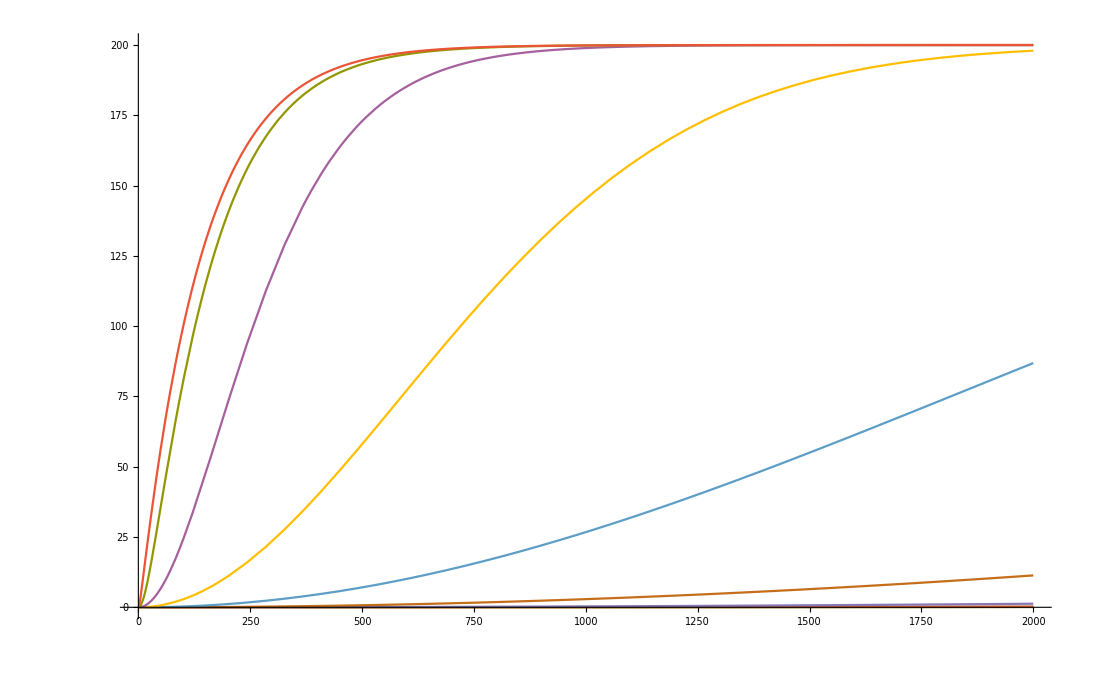

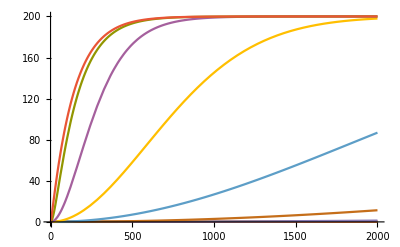

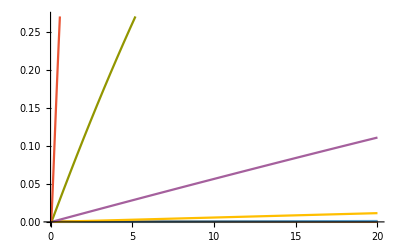

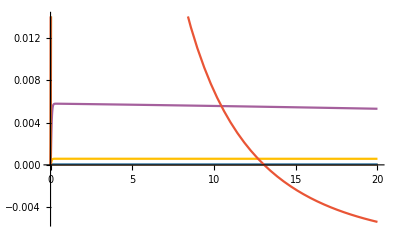

InterpolatingFunction::dmval: Input value {2661.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMaxValue::sdprec: Line search unable to find a sufficient increase in the function value with MachinePrecision digit precision.

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaxValue::lstol will be suppressed during this calculation.

{0.0000923117,0.000113721,0.000120175,0.000228258,100459.,12055.2,46268.,0.193269,0.508832,0.954921,1.25844}

InterpolatingFunction::dmval: Input value {-19.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaxValue::lstol will be suppressed during this calculation.

{5.63295×10^-8,5.69088×10^-8,6.21222×10^-8,1.14256×10^-7,6.35597×10^-7,5.84899×10^-6,0.0000579813,0.000579226,0.00578584,0.0574336,0.546279}

```mathematica
(*a4u6 = 1000, CARFkcat=0*)
resultTable=Evaluate@Table[getProduct[b,1000,0],Evaluate@viralSweep]
Plot[Evaluate@Map[Function[x,x[t]],resultTable, {2}],{t, 0, 2000}, PlotRange->{0,200}]
Plot[Evaluate@Map[Function[x,x[t]],resultTable, {2}],{t, 0, 2000}]
Plot[Evaluate@Map[Function[x,x'[t]],resultTable, {2}],{t, 0, 20}]
Plot[Evaluate@Map[Function[x,x''[t]],resultTable, {2}],{t, 0, 20}]
Map[Function[y, FindMaxValue[y,t]],Map[Function[x,x'[t]],resultTable, {2}]]
Map[Function[y, FindMaxValue[y,t]],Map[Function[x,x''[t]],resultTable, {2}]]
```

{{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]}}

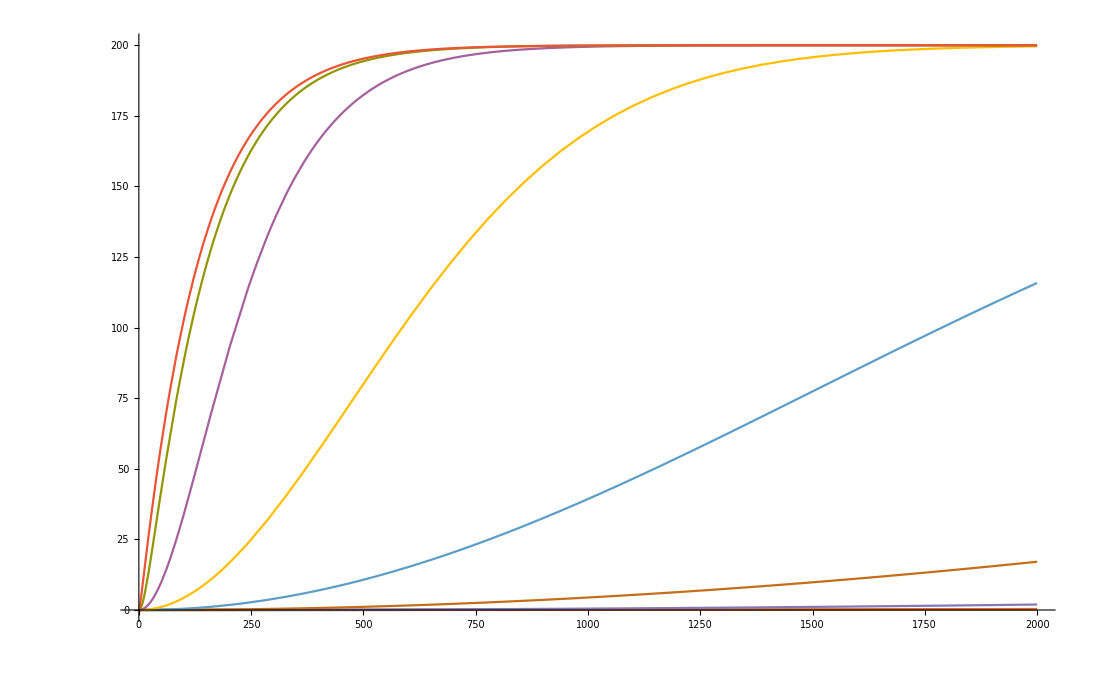

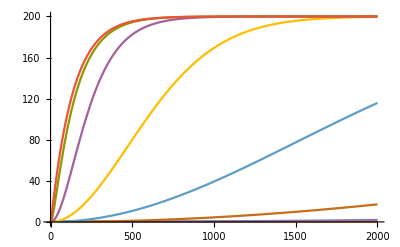

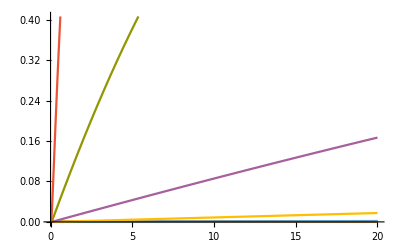

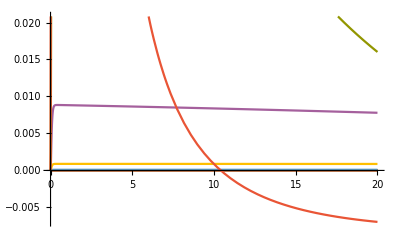

InterpolatingFunction::dmval: Input value {2661.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaxValue::lstol will be suppressed during this calculation.

{0.000172196,0.000173981,3.29715×10^6,0.000349048,0.00192594,4.719×10^7,0.0782539,0.235968,0.597133,1.04425,1.31853}

InterpolatingFunction::dmval: Input value {-19.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaxValue::lstol will be suppressed during this calculation.

{8.61727×10^-8,8.70592×10^-8,9.50373×10^-8,1.74819×10^-7,9.72633×10^-7,8.95074×10^-6,0.0000887282,0.00088631,0.00884735,0.0874054,0.807203}

```mathematica
(*a4u6 = 2000, CARFkcat=0*)
resultTable=Evaluate@Table[getProduct[b,2000,0],Evaluate@viralSweep]
Plot[Evaluate@Map[Function[x,x[t]],resultTable, {2}],{t, 0, 2000}, PlotRange->{0,200}]
Plot[Evaluate@Map[Function[x,x[t]],resultTable, {2}],{t, 0, 2000}]
Plot[Evaluate@Map[Function[x,x'[t]],resultTable, {2}],{t, 0, 20}]
Plot[Evaluate@Map[Function[x,x''[t]],resultTable, {2}],{t, 0, 20}]
Map[Function[y, FindMaxValue[y,t]],Map[Function[x,x'[t]],resultTable, {2}]]
Map[Function[y, FindMaxValue[y,t]],Map[Function[x,x''[t]],resultTable, {2}]]
```

{{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]}}

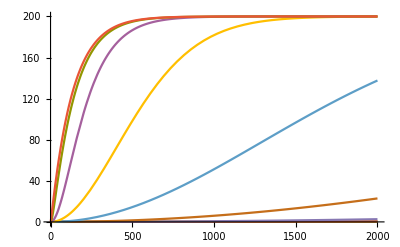

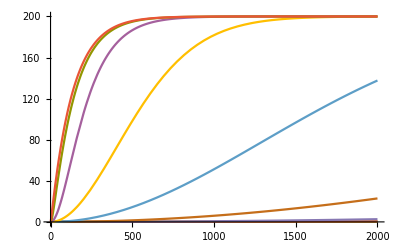

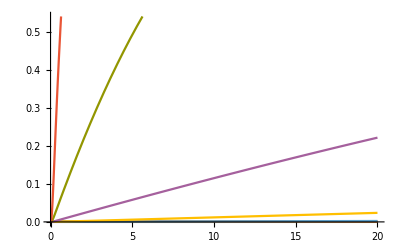

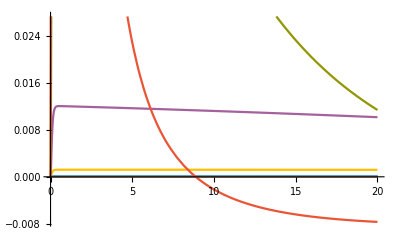

InterpolatingFunction::dmval: Input value {2661.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaxValue::sdprec: Line search unable to find a sufficient increase in the function value with MachinePrecision digit precision.

General::stop: Further output of FindMaxValue::sdprec will be suppressed during this calculation.

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaxValue::lstol will be suppressed during this calculation.

{1.80001×10^12,6.9785×10^6,3.17815×10^11,1.20197×10^19,9422.88,172153.,0.0921733,0.271491,0.662658,1.10016,1.35063}

InterpolatingFunction::dmval: Input value {-19.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaxValue::lstol will be suppressed during this calculation.

{1.1739×10^-7,1.18595×10^-7,1.2944×10^-7,2.37883×10^-7,1.32232×10^-6,0.0000121666,0.000120603,0.00120451,0.0120091,0.117651,1.03614}

```mathematica
(*a4u6 = 4000, CARFkcat=0*)
resultTable=Evaluate@Table[getProduct[b,4000,0],Evaluate@viralSweep]
Plot[Evaluate@Map[Function[x,x[t]],resultTable, {2}],{t, 0, 2000}, PlotRange->{0,200}]
Plot[Evaluate@Map[Function[x,x[t]],resultTable, {2}],{t, 0, 2000}]
Plot[Evaluate@Map[Function[x,x'[t]],resultTable, {2}],{t, 0, 20}]
Plot[Evaluate@Map[Function[x,x''[t]],resultTable, {2}],{t, 0, 20}]
Map[Function[y, FindMaxValue[y,t]],Map[Function[x,x'[t]],resultTable, {2}]]
Map[Function[y, FindMaxValue[y,t]],Map[Function[x,x''[t]],resultTable, {2}]]
```

{{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]}}

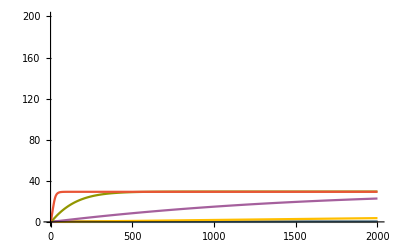

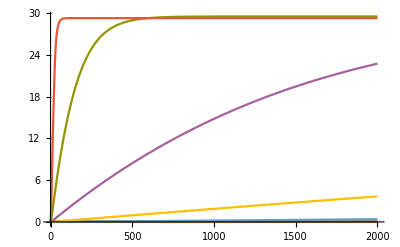

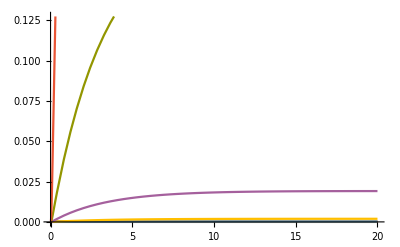

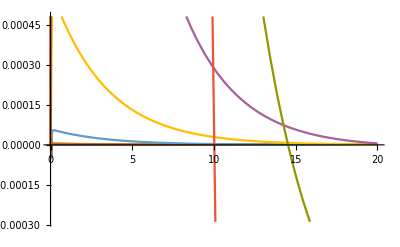

InterpolatingFunction::dmval: Input value {-2179.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{1.8779×10^-7,1.90075×10^-7,2.07268×10^-7,3.80903×10^-7,2.11907×10^-6,0.0000195333,0.000193499,0.00193201,0.0191303,0.178909,1.02519}

InterpolatingFunction::dmval: Input value {-19.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaxValue::lstol will be suppressed during this calculation.

{5.24525×10^-8,5.30038×10^-8,5.79661×10^-8,1.07604×10^-7,6.04062×10^-7,5.5687×10^-6,0.0000552148,0.000551653,0.00551377,0.0549112,0.528484}

```mathematica
(*a4u6 = 1000, CARFkcat=0.5*)
resultTable=Evaluate@Table[getProduct[b,1000,0.5],Evaluate@viralSweep]
Plot[Evaluate@Map[Function[x,x[t]],resultTable, {2}],{t, 0, 2000}, PlotRange->{0,200}]
Plot[Evaluate@Map[Function[x,x[t]],resultTable, {2}],{t, 0, 2000}]
Plot[Evaluate@Map[Function[x,x'[t]],resultTable, {2}],{t, 0, 20}]
Plot[Evaluate@Map[Function[x,x''[t]],resultTable, {2}],{t, 0, 20}]
Map[Function[y, FindMaxValue[y,t]],Map[Function[x,x'[t]],resultTable, {2}]]
Map[Function[y, FindMaxValue[y,t]],Map[Function[x,x''[t]],resultTable, {2}]]
```

{{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]}}

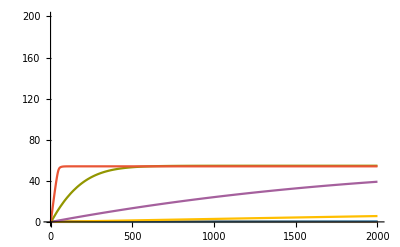

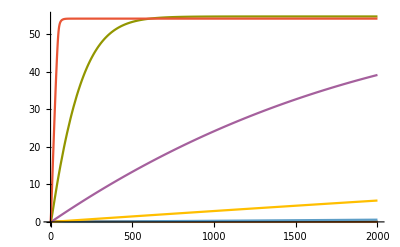

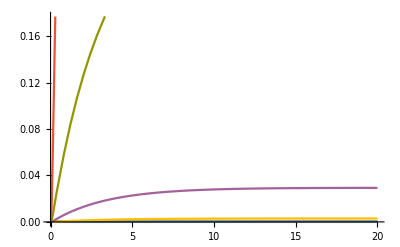

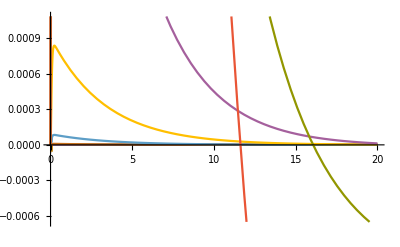

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

InterpolatingFunction::dmval: Input value {-387.835} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaxValue::lstol will be suppressed during this calculation.

{2.87305×10^-7,2.90349×10^-7,3.16835×10^-7,5.83895×10^-7,3.24273×10^-6,0.0000298927,0.00029609,0.00295748,0.0293377,0.276712,1.2435}

InterpolatingFunction::dmval: Input value {-19.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaxValue::lstol will be suppressed during this calculation.

{7.98264×10^-8,8.06605×10^-8,8.81686×10^-8,1.63296×10^-7,9.14769×10^-7,8.4296×10^-6,0.0000835773,0.000834997,0.00834353,0.0828705,0.779204}

```mathematica
(*a4u6 = 2000, CARFkcat=0.5*)
resultTable=Evaluate@Table[getProduct[b,2000,0.5],Evaluate@viralSweep]
Plot[Evaluate@Map[Function[x,x[t]],resultTable, {2}],{t, 0, 2000}, PlotRange->{0,200}]
Plot[Evaluate@Map[Function[x,x[t]],resultTable, {2}],{t, 0, 2000}]
Plot[Evaluate@Map[Function[x,x'[t]],resultTable, {2}],{t, 0, 20}]
Plot[Evaluate@Map[Function[x,x''[t]],resultTable, {2}],{t, 0, 20}]
Map[Function[y, FindMaxValue[y,t]],Map[Function[x,x'[t]],resultTable, {2}]]
Map[Function[y, FindMaxValue[y,t]],Map[Function[x,x''[t]],resultTable, {2}]]
```

{{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]}}

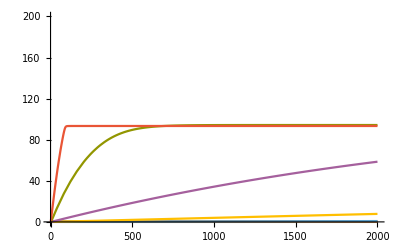

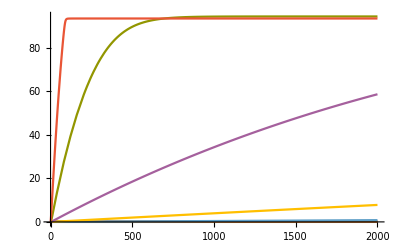

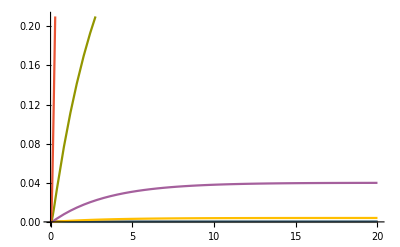

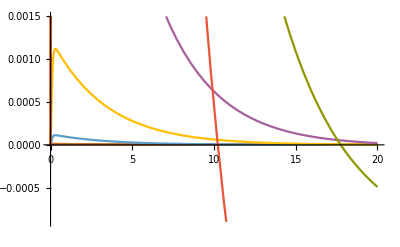

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

InterpolatingFunction::dmval: Input value {-2136.26} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaxValue::lstol will be suppressed during this calculation.

{3.91471×10^-7,3.95386×10^-7,4.31537×10^-7,7.93136×10^-7,4.40969×10^-6,0.0000406336,0.000402786,0.00402078,0.0399326,0.378447,1.31678}

InterpolatingFunction::dmval: Input value {-19.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaxValue::lstol will be suppressed during this calculation.

{1.07966×10^-7,1.09057×10^-7,1.18926×10^-7,2.18696×10^-7,1.21997×10^-6,0.0000112344,0.000111378,0.00111269,0.0111133,0.109896,0.996049}

```mathematica
(*a4u6 = 4000, CARFkcat=0.5*)
resultTable=Evaluate@Table[getProduct[b,4000,0.5],Evaluate@viralSweep]
Plot[Evaluate@Map[Function[x,x[t]],resultTable, {2}],{t, 0, 2000}, PlotRange->{0,200}]
Plot[Evaluate@Map[Function[x,x[t]],resultTable, {2}],{t, 0, 2000}]
Plot[Evaluate@Map[Function[x,x'[t]],resultTable, {2}],{t, 0, 20}]
Plot[Evaluate@Map[Function[x,x''[t]],resultTable, {2}],{t, 0, 20}]
Map[Function[y, FindMaxValue[y,t]],Map[Function[x,x'[t]],resultTable, {2}]]
Map[Function[y, FindMaxValue[y,t]],Map[Function[x,x''[t]],resultTable, {2}]]
```

{{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]}}

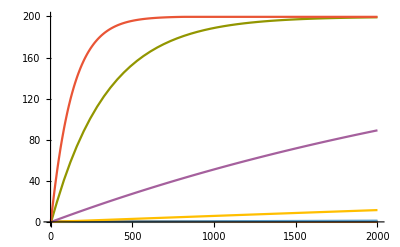

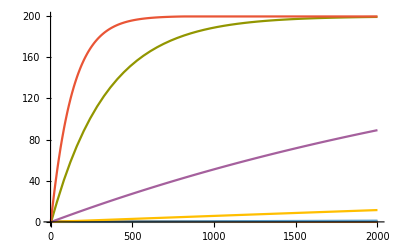

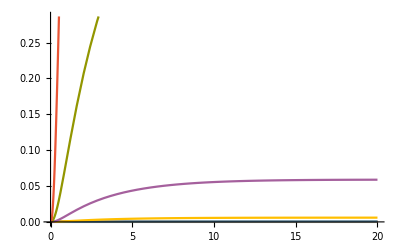

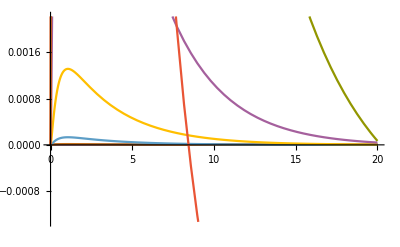

InterpolatingFunction::dmval: Input value {-802.426} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{5.89803×10^-7,5.95788×10^-7,6.48992×10^-7,1.18407×10^-6,6.52241×10^-6,0.0000599021,0.00059367,0.00592035,0.0588563,0.553521,1.36333}

InterpolatingFunction::dmval: Input value {-19.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaxValue::lstol will be suppressed during this calculation.

{1.58098×10^-7,1.58762×10^-7,1.65401×10^-7,2.68416×10^-7,1.44499×10^-6,0.0000132639,0.000131454,0.00131281,0.0130712,0.125307,0.909049}

```mathematica
(*a4u6 = 40000, CARFkcat=0.5*)
resultTable=Evaluate@Table[getProduct[b,40000,0.5],Evaluate@viralSweep]
Plot[Evaluate@Map[Function[x,x[t]],resultTable, {2}],{t, 0, 2000}, PlotRange->{0,200}]
Plot[Evaluate@Map[Function[x,x[t]],resultTable, {2}],{t, 0, 2000}]
Plot[Evaluate@Map[Function[x,x'[t]],resultTable, {2}],{t, 0, 20}]
Plot[Evaluate@Map[Function[x,x''[t]],resultTable, {2}],{t, 0, 20}]
Map[Function[y, FindMaxValue[y,t]],Map[Function[x,x'[t]],resultTable, {2}]]
Map[Function[y, FindMaxValue[y,t]],Map[Function[x,x''[t]],resultTable, {2}]]
```

{{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]},{InterpolatingFunction[{{0., 2000.}}, <>]}}

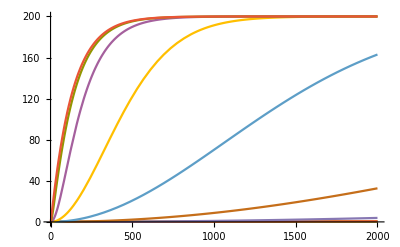

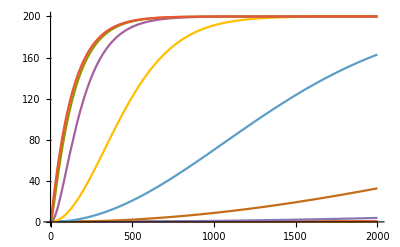

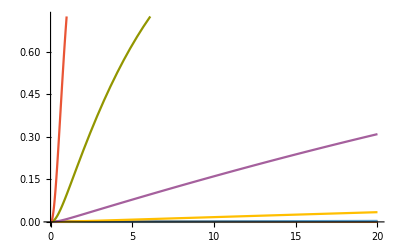

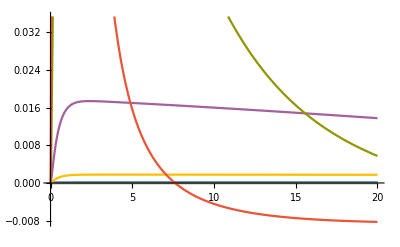

InterpolatingFunction::dmval: Input value {2661.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMaxValue::sdprec: Line search unable to find a sufficient increase in the function value with MachinePrecision digit precision.

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaxValue::lstol will be suppressed during this calculation.

{0.000352988,9.14115×10^6,0.000388658,3.82872×10^13,1560.34,3.34746×10^12,1.20729×10^12,0.32225,0.744998,1.16028,1.3792}

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaxValue::lstol will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-29.9822} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{1.76405×10^-7,1.77986×10^-7,1.9222×10^-7,3.5451×10^-7,1.95279×10^-6,0.0000179317,0.000177337,0.00173301,0.0173656,0.154733,0.976128}

```mathematica
(*a4u6 = 40000, CARFkcat=0*)
resultTable=Evaluate@Table[getProduct[b,40000,0],Evaluate@viralSweep]
Plot[Evaluate@Map[Function[x,x[t]],resultTable, {2}],{t, 0, 2000}, PlotRange->{0,200}]
Plot[Evaluate@Map[Function[x,x[t]],resultTable, {2}],{t, 0, 2000}]
Plot[Evaluate@Map[Function[x,x'[t]],resultTable, {2}],{t, 0, 20}]
Plot[Evaluate@Map[Function[x,x''[t]],resultTable, {2}],{t, 0, 20}]
Map[Function[y, FindMaxValue[y,t]],Map[Function[x,x'[t]],resultTable, {2}]]
Map[Function[y, FindMaxValue[y,t]],Map[Function[x,x''[t]],resultTable, {2}]]
```